```mathematica
Quit[]
```

The notebook is particularized for theory A. For other theories, change ϕM and/or ϕQ. Bear in mind that some FindRoots in finding turning points and stability changing points may require a better guess for other theories.

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->18};
texTicks[min_,max_,step_]:=Table[{x,MaTeX[ToString[x,InputForm]]},{x,min,max,step}];
```

/Users/mikel/Claude files/Spinodal Instabilities code

## Parameters (To be run)

### Scalar potential

```mathematica
constants = {κ-> 1,ϕM->8/10(*9/10*)(*1*),ϕQ-> 10,𝒶-> 0};
(*{κ-> 1,ϕM->1,ϕQ-> 10,𝒶-> 0}*)
V[ϕ_]:=-3-(3 ϕ^2)/2-ϕ^4/3-(4 𝒶^2 ϕ^16)/3+2/3 ϕ^12 (𝒶 (1/ϕM^2+72/ϕQ)-2/ϕQ^2)+ϕ^6 (1/(2 ϕM^4)-1/(3 ϕM^2)-2/ϕQ)+(8 𝒶 ϕ^14 (-1+12 𝒶 ϕQ))/(3 ϕQ)+ϕ^8 (-4 𝒶-(72 ϕM^2-16 ϕM^4+ϕQ)/(12 ϕM^4 ϕQ))+ϕ^10 (𝒶 (4/3-8/ϕM^2)+(2 (27+ϕQ/ϕM^2))/(3 ϕQ^2))/.constants
```

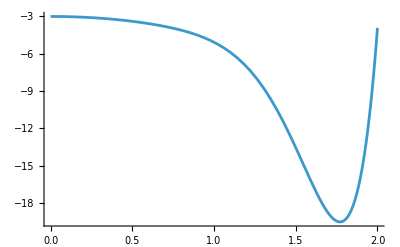

```mathematica
Plot[V[ϕ],{ϕ,0,2}]
```

### Numerical parameters

```mathematica
(* ---- Backgrounds ---- *)
Nz = 80; precision = 100;                      (* radial Gauss-Lobatto points, working precision *)
λ = 1; tol = 10^(-precision); maxit = 19;      (* Newton relaxation *)
{ψHmin, ψHmax, NψH} = {5/10,177/100,200};  (* range and number of backgrounds *)

(* ---- Phase diagram: FindRoot guesses ---- *)
ψHturningGuess = {1, 16/10};    (* T'(ψH) = 0, the two spinodal points *)
stabilitySwitch = True;         (* False if s'(ψH) has no roots in the range *)
ψHstabilityGuess = {1, 16/10};  (* s'(ψH) = 0, only used if stabilitySwitch *)

(* ---- Log-scale momentum grid: 2π q from 10^nmin to 10^nmax ---- *)
Nq = 10; {nmin, nmax} = {-6, -1};

(* ---- Backgrounds shown in the plots as a function of q ---- *)
ψHplot = {0.67, 0.87, 1.05, 1.29, 1.56, 1.73};
```

```mathematica
tag = "phiM=" <> ToString[N[ϕM /. constants]] <> "_phiQ=" <> ToString[N[ϕQ /. constants]] <> "_a=" <> ToString[N[𝒶 /. constants]];
backgroundFile = "./background_data/" <> tag <> "_N_" <> ToString[Nz] <> "_" <> ToString[NψH] <> "_backgrounds.m";
qnmFile = "./QNM_data/QNMs_" <> tag <> "_Nz_" <> ToString[Nz] <> "_NpsiH_" <> ToString[NψH] <> "_Nq_" <> ToString[Nq] <> ".m";
figsDir = "./figs/";
Quiet[CreateDirectory /@ {"./background_data", "./QNM_data", figsDir}];
{backgroundFile, qnmFile}
```

{./background_data/phiM=0.8_phiQ=10._a=0._N_80_200_backgrounds.m,./QNM_data/QNMs_phiM=0.8_phiQ=10._a=0._Nz_80_NpsiH_200_Nq_10.m}

## Routines

### Backgrounds

Going from r coordinate to compact and back. Gauss-Lobato grid. Adapted from Trefethen.

```mathematica
Cheb[xmin_,xmax_,Nu_,prec_]:=Block[{M,x,c,X,ΔX,D,D2},
			M=Nu-1;
			x = -Cos[π Range[0,M]/M];
			c = (-1)^Range[0,M] Join[{2},Table[1,{ii,1,M-1}],{2}];
			X = Table[x,{ii,1,Nu}]ᵀ;        
			ΔX = X-Xᵀ;
			D=({c}ᵀ.{c}^-1)/(ΔX+IdentityMatrix@Nu);
			D = D-DiagonalMatrix@Total[Dᵀ];
			x = 1/2 (xmax+xmin+(xmax-xmin) x); 
			D = (2 D)/(xmax-xmin);
			SetPrecision[{x, D, D.D},prec]];
			
(*FiniteDiff2nd[xmin_,xmax_,Nx_] := Block[{δx,x,D,D2},
			δx = (xmax-xmin)/(Nx-1);
			x = Range[xmin,xmax,δx]; 
			D = 0 IdentityMatrix[Nx];
			D2 = 0 IdentityMatrix[Nx];
			Do[
			D[[i,i-1;;i+1]] = {-1,0,1}//Flatten;
			D2[[i,i-1;;i+1]] = {1,-2,1}//Flatten;
			,{i,2,Nx-1}];
			D[[1,1;;3]] = {-3,4,-1}//Flatten;
			D2[[1,1;;3]] = {1,-2,1}//Flatten;
			D[[Nx,Nx-2;;Nx]] = {1,-4,3}//Flatten; 
			D2[[Nx,Nx-2;;Nx]] = {1,-2,1}//Flatten;
			{x, 1/(2δx)D, 1/δx^2 D2}];*)
```

Coefficients

```mathematica
A11[r_,g0_] := r g0 
B11[r_,D_,g0_] := -3 g0+2 r D.g0
B12[r_,D_,f0_]:= 2 r D.f0
C12[r_,D_,D2_,f0_]:= -3 D.f0+r D2.f0
S1[r_,D_,D2_,f0_,g0_]:= 2 r D.f0 D.g0+g0 (-3 D.f0+r D2.f0)

A22[r_,g0_] := -3 r g0
B22[r_,D_,g0_] := -3 g0+6 r D.g0
B23[r_,D_,g0_,ψ0_]:= -8 r^2 g0^2 (ψ0+r D.ψ0)
C22[r_,D_,D2_,g0_,ψ0_]:= -8 r g0 (ψ0+r D.ψ0)^2-3 (D.g0+r D2.g0)
C23[r_,D_,D2_,g0_,ψ0_]:= -8 r g0^2 (ψ0+r D.ψ0)
S2[r_,D_,D2_,g0_,ψ0_]:= 3 r (D.g0)^2-4 r g0^2 (ψ0+r D.ψ0)^2-3 g0 (D.g0+r D2.g0)


A33[r_,f0_] := r^3 f0;
B31[r_,D_,ψ0_]:= r^2 (ψ0+r D.ψ0)
B32[r_,D_,f0_,g0_,ψ0_] := (2 r^2 f0 (ψ0+r D.ψ0))/g0
B33[r_,D_,f0_,g0_]:= r^2 (r D.f0+f0 (-1+(2 r D.g0)/g0))
C31[r_,D_,D2_,g0_,ψ0_]:=r (-3 ψ0+(2 r D.g0 (ψ0+r D.ψ0))/g0+r (-D.ψ0+r D2.ψ0))
C32[r_,D_,f0_,g0_,ψ0_]:= -(2 r^2 f0 D.g0 (ψ0+r D.ψ0))/g0^2
C33[r_,D_,f0_,g0_,ψ0_,VV_]:= r (r D.f0+f0(-3+(2 r D.g0)/g0)-VV''[r ψ0])
S3[r_,D_,D2_,f0_,g0_,ψ0_,VV_]:= -VV'[r ψ0]+r (r D.f0 (ψ0+r D.ψ0)+f0 ((-3+(2 r D.g0)/g0) (ψ0+r D.ψ0)+r (2 D.ψ0+r D2.ψ0)))

BH11[D_,ψ0_]:= ψ0[[-1]]+D[[-1,;;]].ψ0
BH13[D_,f0_] := D[[-1,;;]].f0
CH13[D_,f0_,ψ0_,VV_] := D[[-1,;;]].f0-VV''[ψ0[[-1]]]
SH1[D_,f0_,ψ0_,VV_] := -VV'[ψ0[[-1]]]+D[[-1,;;]].f0 (ψ0[[-1]]+D[[-1,;;]].ψ0)

BH21[D_,g0_]:= 3/4 (-2+(D[[-1,;;]].g0)/g0[[-1]])
BH22[D_,f0_,g0_] := (3 D[[-1,;;]].f0)/(4 g0[[-1]])
CH22[D_,f0_,g0_,VV_] := -(3 D[[-1,;;]].f0 D[[-1,;;]].g0)/(4 g0[[-1]]^2)
CH23[ψ0_,VV_]:= 2 VV'[ψ0[[-1]]]
SH2[D_,f0_,g0_,ψ0_,VV_] := 2 VV[ψ0[[-1]]]+(3 D[[-1,;;]].f0 (-2 g0[[-1]]+D[[-1,;;]].g0))/(4 g0[[-1]])
```

```mathematica
MatrixProblem[u_,D_,D2_,f0_,g0_,ψ0_,ψH_,V_]:=Block[{Id,precision,DerivM1,DerivM2,DerivM3,MM,N,v},
				N = Length[u];
				precision = Precision[u];
				Id = IdentityMatrix[N];
				
				MM = ArrayFlatten[{
				{A11[u,g0] D2 + B11[u,D,g0] D,   B12[u,D,f0] D + C12[u,D,D2,f0]Id,   0},
				{0,  A22[u,g0]D2 + B22[u,D,g0]D + C22[u,D,D2,g0,ψ0]Id,      B23[u,D,g0,ψ0]D + C23[u,D,D2,g0,ψ0]Id },
				{B31[u,D,ψ0] D +C31[u,D,D2,g0,ψ0]Id,  B32[u,D,f0,g0,ψ0]D+C32[u,D,f0,g0,ψ0]Id,       A33[u,f0]D2 + B33[u,D,f0,g0]D + C33[u,D,f0,g0,ψ0,V]Id}
				}];
				
				(*BC at boundary, grid point 1*)
				MM⟦1,;;⟧    = 0;    MM⟦1,1⟧     = 1;
				MM⟦N+1,;;⟧  = 0;    MM[[N+1,N+1]] = 1;
				MM⟦2N+1,;;⟧ = 0;    MM[[2N+1,3N]] = 1;
						
				(*Constraints at Horizon*)
				MM⟦N,;;⟧ = 0;    MM[[N,N]] = 1;
				
			    MM⟦2N,;;⟧ = Flatten[{BH11[D,ψ0]D[[N,;;]], 0Id[[N,;;]], BH13[D,f0]D[[N,;;]] + CH13[D,f0,ψ0,V]Id[[N,;;]]}];
			    
			    MM⟦3N,;;⟧ = Flatten[{BH21[D,g0]D[[N,;;]], BH22[D,f0,g0]D[[N,;;]] + CH22[D,f0,g0,V]Id[[N,;;]], CH23[ψ0,V]Id[[N,;;]]}];
			    
				v=Join[{1-f0[[1]]},-S1[u,D,D2,f0,g0]⟦2;;N-1⟧,{-f0[[N]]},{1-g0[[1]]},-S2[u,D,D2,g0,ψ0]⟦2;;N-1⟧,{-SH1[D,f0,ψ0,V]},{ψH-ψ0[[N]]},-S3[u,D,D2,f0,g0,ψ0,V]⟦2;;N-1⟧,{-SH2[D,f0,g0,ψ0,V]}];
				
				SetPrecision[{MM,v},precision]];
				
Relaxation[u_,D_,D2_,ψH_,fg_,gg_,ψg_,V_,λ_,tol_,maxit_]:=Block[{N,f,g,ψ,M,v,sol,res,it},
			N = Length[u];
		    f = fg;    g = gg;    ψ = ψg;
			res = Max[Abs[Join[{1-f[[1]]},-S1[u,D,D2,f,g]⟦2;;N-1⟧,{-f[[N]]},{1-g[[1]]},S2[u,D,D2,g,ψ]⟦2;;N-1⟧,{SH1[D,f,ψ,V]},{ψH-ψ[[N]]},-S3[u,D,D2,f,g,ψ,V]⟦1;;N-1⟧,{SH2[D,f,g,ψ,V]}]]];
			it = 1;
			Monitor[While[res ≥  tol && it ≤ maxit,
				{M,v} = MatrixProblem[u,D,D2,f,g,ψ,ψH,V];
				sol = LinearSolve[M,v];
				f += λ sol⟦1;;N⟧;     g += λ sol⟦N+1;;2N⟧;    ψ += λ sol⟦2N+1;;3N⟧;
				res = Max[Abs[Join[{1-f[[1]]},-S1[u,D,D2,f,g]⟦2;;N-1⟧,{-f[[N]]},{1-g[[1]]},S2[u,D,D2,g,ψ]⟦2;;N-1⟧,{SH1[D,f,ψ,V]},{ψH-ψ[[N]]},-S3[u,D,D2,f,g,ψ,V]⟦1;;N-1⟧,{SH2[D,f,g,ψ,V]}]]];
				it += 1;],{it, res}];
				(*Print[{it, res}];*)
			{f,g,ψ}];
```

### Quasinormal modes

Coefficients for the equations: (M0 + M1 ω ) Φ = 0 . Already with ingoing boundary conditions. With Mi = 𝒜i . {D2,D,Id}. In Φ first Zφ and second Z2: Φ = {Z_φ Z_2}

```mathematica
𝒜[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_]:={{{6 f^2 g^3 π^2 q^2 T^2 u^3 (2 g-u D.g) (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ]),0},{0,9 f g^2 π^2 q^2 T^2 u^2 (-2 g+u D.g)^2 (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ])}},{{0,0},{0,0}},{{54 f^2 g^3 π^2 T^2 u^3 (-2 g+u D.g)^3,0},{0,-81 f g^2 π^2 T^2 u^2 (-2 g+u D.g)^4}},{{0,0},{0,0}}};
```

```mathematica
ℬ[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_]:={{{2 f g^3 π^2 q^2 T^2 u^2 (-9 f u D.g-2 f g (-9+2 u^2 ψ^2+4 u^3 ψ D.ψ+2 u^4 (D.ψ)^2)+8 g V[u ψ]) (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ]),-3 f g^3 u (-2 g+u D.g) (8 g u (ψ+u D.ψ) V[u ψ]+3 (-2 g+u D.g) V'[u ψ])},{0,3 g π^2 q^2 T^2 u (-2 g+u D.g) (f^2 (-171 g u^3 (D.g)^3+18 u^4 (D.g)^4+6 g^2 u^2 (D.g)^2 (99+2 u^2 ψ^2+4 u^3 ψ D.ψ+2 u^4 (D.ψ)^2)-12 g^3 u D.g (75+7 u^2 ψ^2+14 u^3 ψ D.ψ+7 u^4 (D.ψ)^2)-8 g^4 (-63-15 u^2 ψ^2+2 u^4 ψ^4+(-30 u^3 ψ+8 u^5 ψ^3) D.ψ+3 u^4 (-5+4 u^2 ψ^2) (D.ψ)^2+8 u^7 ψ (D.ψ)^3+2 u^8 (D.ψ)^4))+72 f g^2 (2 g^2-3 g u D.g+u^2 (D.g)^2) V[u ψ]+64 g^4 V[u ψ]^2)}},{{24 ⅈ f g^(5/2) π^3 q^2 T^3 u^3 (2 g-u D.g) (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ]),0},{0,-36 ⅈ g^(3/2) π^3 q^2 T^3 u^2 (2 g-u D.g) (-2 g+u D.g) (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ])}},{{18 f g^3 π^2 T^2 u^2 (-2 g+u D.g)^2 (9 f u D.g+2 f g (-9+2 u^2 ψ^2+4 u^3 ψ D.ψ+2 u^4 (D.ψ)^2)-8 g V[u ψ]),0},{0,-27 g π^2 T^2 u (-2 g+u D.g)^3 (f (15 g u D.g-6 u^2 (D.g)^2+g^2 (-6+4 u^2 ψ^2+8 u^3 ψ D.ψ+4 u^4 (D.ψ)^2))-8 g^2 V[u ψ])}},{{216 ⅈ f g^(5/2) π^3 T^3 u^3 (-2 g+u D.g)^3,0},{0,-324 ⅈ g^(3/2) π^3 T^3 u^2 (-2 g+u D.g)^4}}};
```

```mathematica
𝒞[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_]:={{{2 f g^2 π^2 T^2 u (36 f π^2 q^4 T^2 u^5 (D.g)^3+6 g^2 u^2 D.g (8 π^2 q^4 T^2 u (9 f+f u^2 ψ^2+2 f u^3 ψ D.ψ+f u^4 (D.ψ)^2-2 V[u ψ])+f q^2 D.g (9 f-2 f u^2 ψ^2-2 f u^4 (D.ψ)^2+4 V[u ψ]-4 u^2 D.ψ (f u ψ-4 V'[u ψ])+16 u ψ V'[u ψ]-9 V''[u ψ]))-9 f g q^2 u^3 (D.g)^2 (24 π^2 q^2 T^2 u+D.g (f-V''[u ψ]))+8 g^4 q^2 (-f^2 (-9+3 u^2 ψ^2+2 u^4 ψ^4+(6 u^3 ψ+8 u^5 ψ^3) D.ψ+3 (u^4+4 u^6 ψ^2) (D.ψ)^2+8 u^7 ψ (D.ψ)^3+2 u^8 (D.ψ)^4)-8 V[u ψ]^2-2 V[u ψ] (4 u (ψ+u D.ψ) V'[u ψ]-3 V''[u ψ])+f (-2 (-3+20 u^2 ψ^2+40 u^3 ψ D.ψ+20 u^4 (D.ψ)^2) V[u ψ]+4 u (ψ (12+u^2 ψ^2)+3 u (4+u^2 ψ^2) D.ψ+3 u^4 ψ (D.ψ)^2+u^5 (D.ψ)^3) V'[u ψ]-3 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2) V''[u ψ]))-12 g^3 u (8 π^2 q^4 T^2 u (f (3+u^2 ψ^2)+2 f u^3 ψ D.ψ+f u^4 (D.ψ)^2-2 V[u ψ])-q^2 D.g (2 V[u ψ] (f (-3+8 u^2 ψ^2)-V''[u ψ])+f u^4 (D.ψ)^2 (3 f+16 V[u ψ]+V''[u ψ])+f (3 f (-3+u^2 ψ^2)-32 u ψ V'[u ψ]+(9+u^2 ψ^2) V''[u ψ])+2 f u^2 D.ψ (16 u ψ V[u ψ]-16 V'[u ψ]+u ψ (3 f+V''[u ψ]))))),2 g^3 (3 f u D.g+f g (-6+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2)-2 g V[u ψ]) (8 g u (ψ+u D.ψ) V[u ψ]+3 (-2 g+u D.g) V'[u ψ])},{-64 g^3 π^4 q^4 T^4 u (f (12 g u D.g-3 u^2 (D.g)^2+2 g^2 (-6+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-4 g^2 V[u ψ]) (24 f g u (2 g-u D.g) (ψ+u D.ψ) V[u ψ]-f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2)) V'[u ψ]+8 g^2 V[u ψ] V'[u ψ]),π^2 T^2 (27 f^2 q^2 u^6 (D.g)^6-108 f g q^2 u^5 (D.g)^4 (π^2 q^2 T^2 u+4 f D.g)+64 g^6 q^2 (f^2 (108+9 u^2 ψ^2-6 u^4 ψ^4+u^6 ψ^6+6 u^3 ψ (3-4 u^2 ψ^2+u^4 ψ^4) D.ψ+3 u^4 (3-12 u^2 ψ^2+5 u^4 ψ^4) (D.ψ)^2+4 u^7 ψ (-6+5 u^2 ψ^2) (D.ψ)^3+3 u^8 (-2+5 u^2 ψ^2) (D.ψ)^4+6 u^11 ψ (D.ψ)^5+u^12 (D.ψ)^6)-2 f (-36-3 u^2 ψ^2+2 u^4 ψ^4+(-6 u^3 ψ+8 u^5 ψ^3) D.ψ+3 u^4 (-1+4 u^2 ψ^2) (D.ψ)^2+8 u^7 ψ (D.ψ)^3+2 u^8 (D.ψ)^4) V[u ψ]+4 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2) V[u ψ]^2)-72 g^3 u^3 (D.g)^2 (2 π^2 q^4 T^2 u (18 f+f u^2 ψ^2+2 f u^3 ψ D.ψ+f u^4 (D.ψ)^2-2 V[u ψ])+f q^2 D.g (132 f-3 f u^2 ψ^2-6 f u^3 ψ D.ψ-3 f u^4 (D.ψ)^2+22 V[u ψ]))-48 g^4 q^2 u^2 D.g (-12 π^2 q^2 T^2 u (f (6+u^2 ψ^2)+2 f u^3 ψ D.ψ+f u^4 (D.ψ)^2-2 V[u ψ])+f D.g (f (-369+6 u^2 ψ^2+u^4 ψ^4)+4 f u^7 ψ (D.ψ)^3+f u^8 (D.ψ)^4+4 u^3 ψ D.ψ (f (3+u^2 ψ^2)-V[u ψ])+2 u^4 (D.ψ)^2 (3 (f+f u^2 ψ^2)-V[u ψ])-2 (60+u^2 ψ^2) V[u ψ]))-36 f g^2 q^2 u^4 (D.g)^3 (f D.g (-78+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2)-4 (6 π^2 q^2 T^2 u+D.g V[u ψ]))-96 g^5 q^2 u (6 π^2 q^2 T^2 u (f (3+u^2 ψ^2)+2 f u^3 ψ D.ψ+f u^4 (D.ψ)^2-2 V[u ψ])+D.g (3 f^2 (60+u^2 ψ^2-u^4 ψ^4)-12 f^2 u^7 ψ (D.ψ)^3-3 f^2 u^8 (D.ψ)^4+2 f (45+2 u^2 ψ^2) V[u ψ]+4 V[u ψ]^2+2 f u^3 ψ D.ψ (3 f-6 f u^2 ψ^2+4 V[u ψ])+f u^4 (D.ψ)^2 (3 f (1-6 u^2 ψ^2)+4 V[u ψ]))))}},{{-6 ⅈ f g^(3/2) π^3 q^2 T^3 u^2 (4 g^2-8 g u D.g+3 u^2 (D.g)^2) (f (-12 g u D.g+3 u^2 (D.g)^2+4 g^2 (3+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-8 g^2 V[u ψ]),-6 ⅈ g^(5/2) π T u (-2 g+u D.g) (8 g u (ψ+u D.ψ) V[u ψ]+3 (-2 g+u D.g) V'[u ψ])},{0,3 ⅈ √g π^3 q^2 T^3 u (2 g-u D.g) (f (576 g u^3 (D.g)^3-63 u^4 (D.g)^4+240 g^3 u D.g (12+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2)-36 g^2 u^2 (D.g)^2 (54+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2)+16 g^4 (-99-21 u^2 ψ^2+4 u^4 ψ^4+2 u^3 ψ (-21+8 u^2 ψ^2) D.ψ+3 u^4 (-7+8 u^2 ψ^2) (D.ψ)^2+16 u^7 ψ (D.ψ)^3+4 u^8 (D.ψ)^4))-8 g^2 (-36 g u D.g+15 u^2 (D.g)^2+4 g^2 (3+4 u^2 ψ^2+8 u^3 ψ D.ψ+4 u^4 (D.ψ)^2)) V[u ψ])}},{{-6 f g^2 π^2 T^2 u (-2 g+u D.g) (36 π^2 q^2 T^2 u^4 (D.g)^2-9 g u^2 D.g (16 π^2 q^2 T^2 u+D.g (f-V''[u ψ]))+4 g^3 (3 f (-3+2 u^2 ψ^2+4 u^3 ψ D.ψ+2 u^4 (D.ψ)^2)+4 (-3+4 u^2 ψ^2+8 u^3 ψ D.ψ+4 u^4 (D.ψ)^2) V[u ψ]-24 u (ψ+u D.ψ) V'[u ψ]+9 V''[u ψ])+12 g^2 u (12 π^2 q^2 T^2 u-D.g (-3 f+f u^2 ψ^2+f u^4 (D.ψ)^2-2 V[u ψ]+2 u^2 D.ψ (f u ψ-2 V'[u ψ])-4 u ψ V'[u ψ]+3 V''[u ψ]))),0},{-192 g^2 π^4 q^2 T^4 u (-2 g+u D.g) (f (12 g u D.g-3 u^2 (D.g)^2+2 g^2 (-6+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))-4 g^2 V[u ψ]) (2 f u (ψ+u D.ψ) (12 g u D.g-3 u^2 (D.g)^2+2 g^2 (-6+u^2 ψ^2+2 u^3 ψ D.ψ+u^4 (D.ψ)^2))+3 g (-2 g+u D.g) V'[u ψ]),27 π^2 T^2 u (-2 g+u D.g)^3 (-3 f u^2 (D.g)^3+6 g u D.g (2 π^2 q^2 T^2 u+f D.g)+8 f g^3 u (ψ+u D.ψ)^2-8 g^2 (3 π^2 q^2 T^2 u+D.g V[u ψ]))}},{{54 ⅈ f g^(3/2) π^3 T^3 u^2 (-2 g+u D.g)^3 (-2 g+3 u D.g),0},{0,81 ⅈ √g π^3 T^3 u (-2 g+u D.g)^4 (6 g+u D.g)}}};
```

```mathematica
𝒜H[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_] :={{0,0},{0,0},{0,0},{0,0}};
ℬH[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_] :={{8 π^2 q^2 T^2 (D⟦-1,;;⟧.f)^4 g⟦-1⟧^(3/2) V[ψ⟦-1⟧],0},{32 ⅈ π^3 q^2 T^3 (D⟦-1,;;⟧.f)^3 g⟦-1⟧ V[ψ⟦-1⟧],0},{64 π^2 T^2 (D⟦-1,;;⟧.f)^2 g⟦-1⟧^(3/2) V[ψ⟦-1⟧]^2,0},{256 ⅈ π^3 T^3 D⟦-1,;;⟧.f g⟦-1⟧ V[ψ⟦-1⟧]^2,0}};
𝒞H[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_] :={{-8 π^2 q^2 T^2 (D⟦-1,;;⟧.f)^3 √g⟦-1⟧ (-g⟦-1⟧ V'[ψ⟦-1⟧]^2+V[ψ⟦-1⟧] (4 π^2 q^2 T^2-D⟦-1,;;⟧.f g⟦-1⟧+g⟦-1⟧ V''[ψ⟦-1⟧])),D⟦-1,;;⟧.f √g⟦-1⟧ V'[ψ⟦-1⟧] (V'[ψ⟦-1⟧]^2-V[ψ⟦-1⟧] V''[ψ⟦-1⟧])},{32 ⅈ π^3 q^2 T^3 (D⟦-1,;;⟧.f)^2 g⟦-1⟧ (D⟦-1,;;⟧.f-2 V[ψ⟦-1⟧]) V[ψ⟦-1⟧],-4 ⅈ π T V'[ψ⟦-1⟧] (V'[ψ⟦-1⟧]^2-V[ψ⟦-1⟧] V''[ψ⟦-1⟧])},{-64 π^2 T^2 D⟦-1,;;⟧.f √g⟦-1⟧ V[ψ⟦-1⟧] (-g⟦-1⟧ V'[ψ⟦-1⟧]^2+V[ψ⟦-1⟧] (4 π^2 q^2 T^2-D⟦-1,;;⟧.f g⟦-1⟧+g⟦-1⟧ V''[ψ⟦-1⟧])),0},{-256 ⅈ π^3 T^3 g⟦-1⟧ V[ψ⟦-1⟧]^2 (-D⟦-1,;;⟧.f+2 V[ψ⟦-1⟧]),0}};
```

Build the matrix for a quadratic equation in ω

```mathematica
BuildSeparateMatrices[u_,D_,D2_,f_,g_,ψ_,V_,q_,T_]:= Block[{M0,M1,M2,M3,MAray,N,Id},
										N = Length[u];
										Id = IdentityMatrix[N];
										
										MArray = {};
										
										Do[
											AppendTo[MArray,ArrayFlatten[{
											{𝒜[u,D,D2,f,g,ψ,V,q,T][[n,1,1]]D2+ℬ[u,D,D2,f,g,ψ,V,q,T][[n,1,1]]D+𝒞[u,D,D2,f,g,ψ,V,q,T][[n,1,1]]Id,
											𝒜[u,D,D2,f,g,ψ,V,q,T][[n,1,2]]D2+ℬ[u,D,D2,f,g,ψ,V,q,T][[n,1,2]]D+𝒞[u,D,D2,f,g,ψ,V,q,T][[n,1,2]]Id},
											{𝒜[u,D,D2,f,g,ψ,V,q,T][[n,2,1]]D2+ℬ[u,D,D2,f,g,ψ,V,q,T][[n,2,1]]D+𝒞[u,D,D2,f,g,ψ,V,q,T][[n,2,1]]Id,
											𝒜[u,D,D2,f,g,ψ,V,q,T][[n,2,2]]D2+ℬ[u,D,D2,f,g,ψ,V,q,T][[n,2,2]]D+𝒞[u,D,D2,f,g,ψ,V,q,T][[n,2,2]]Id}}]];
										,{n,1,4}];
										
										M0 = MArray[[1]];
										M1 = MArray[[2]];
										M2 = MArray[[3]];
										M3 = MArray[[4]];
										
										(*Equation at the boundary*)
										M0[[1,;;]]    = 0;  M0[[1,1]]     = 1;
										M0[[N+1,;;]]  = 0;  M0[[N+1,N+1]] = 1;
										
										M1[[1,;;]] = 0; M1[[N+1,;;]] = 0; 
										M2[[1,;;]] = 0; M2[[N+1,;;]] = 0; 
										M3[[1,;;]] = 0; M3[[N+1,;;]] = 0; 
										
										
										M0[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,q,T][[1,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[1,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,q,T][[1,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[1,2]]Id[[-1,;;]] 
										}];
										
										M1[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,q,T][[2,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[2,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,q,T][[2,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[2,2]]Id[[-1,;;]] 
										}];
										
										M2[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,q,T][[3,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[3,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,q,T][[3,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[3,2]]Id[[-1,;;]] 
										}];
										
										M3[[N,;;]] = Flatten[{ℬH[u,D,D2,f,g,ψ,V,q,T][[4,1]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[4,1]]Id[[-1,;;]],
															 ℬH[u,D,D2,f,g,ψ,V,q,T][[4,2]]D[[-1,;;]] + 𝒞H[u,D,D2,f,g,ψ,V,q,T][[4,2]]Id[[-1,;;]] 
										}];

										{M0,M1,M2,M3}];

BuildMatrices[grid_,f_,g_,ψ_,V_,q_,T_]:= Block[{u,N,precision,M0,M1,M2,M3,D,D2,DD,DD2,N1,N2,,ℳ0,ℳ1,Id,IId,ω},
										{u,D,D2}    = grid;
										precision   = Precision[u];
										N           = Length[u];
										IId         = IdentityMatrix[2N];
										
										{M0,M1,M2,M3} = BuildSeparateMatrices[u,D,D2,f,g,ψ,V,q,T];
										
										ℳ0 = ArrayFlatten[{{M0,M1,M2},{0,IId,0},{0,0,IId}}];
										ℳ1 = ArrayFlatten[{{0,0,M3},{-IId,0,0},{0,-IId,0}}];
										
										SetPrecision[{SparseArray[ℳ0],SparseArray[ℳ1]},precision]];

GetQNM[grid1_,fields_,V_,q_,T_,prec_,NQNMs_,eigenfunctions_] := Block[{grid,ℳ0,ℳ1,f,g,ψ},
								{f,g,ψ} = fields;
								{ℳ0,ℳ1} = BuildMatrices[grid1,f,g,ψ,V,q,T];
								If[eigenfunctions,
								SetPrecision[Eigensystem[{SetPrecision[ℳ0,prec],-SetPrecision[ℳ1,prec]}(*,-NQNMs*)],prec],
								SetPrecision[Eigenvalues[{SetPrecision[ℳ0,prec],-SetPrecision[ℳ1,prec]}(*,-NQNMs*)],prec]]];
```

## 1. Backgrounds

To obtain good results for p and e, it is recommended Nu = 80 for theory A. The QNM computation and EFT parameter extraction can be done with 40 points.

### Solve all backgrounds

```mathematica
z = SetPrecision[
   Reverse[Table[1/2 + 1/2 Cos[(j - 1) π/(Nz - 1)], {j, 1, Nz}]], 
   precision];
Dz = NDSolve`FiniteDifferenceDerivative[1, z, 
    "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
Dz2 = NDSolve`FiniteDifferenceDerivative[2, z, 
    "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
ψHlist = 
  SetPrecision[
   Reverse[Table[(ψHmax + ψHmin)/
       2 + (ψHmax - ψHmin)/
        2 Cos[(j - 1) π/(NψH - 1)], {j, 1, NψH}]], 
   precision];
DψH = 
  NDSolve`FiniteDifferenceDerivative[1, ψHlist, 
    "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];

(* local 8th-order finite-difference d/dψH (9-point stencil on ψHlist), used for all thermodynamic derivatives: the global spectral DψH is off by ~1e-4 in d log s/dψH, which near the poles of c_s^2 makes c_s^2 and ζ/s noisy *)
DψHFD = NDSolve`FiniteDifferenceDerivative[1, ψHlist, "DifferenceOrder" -> 8]["DifferentiationMatrix"];
DψH2 = 
  NDSolve`FiniteDifferenceDerivative[2, ψHlist, 
    "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
numbersToPlot = 
  First[Ordering[Abs[ψHlist - #], 1]] & /@ ψHplot;
```

```mathematica
(*Initial guess: Scharwzchild-Subscript[AdS, \
5] with a small scalar field*)
f = Table[1 - z[[i]]^4, {i, 1, Nz}];
g = Table[1, {i, 1, Nz}];
ψ = Table[ψHmin z[[i]], {i, 1, Nz}];

fields = {}; thermo = {};
Monitor[Do[
    ψH = ψHlist[[i]];
    f0 = f; g0 = g; ψ0 = ψ;
    {f, g, ψ} = 
     SetPrecision[
       Relaxation[z, Dz, Dz2, ψH, f0, g0, ψ0, V, λ, 
        tol, maxit], precision] // Quiet;
    AppendTo[fields, {f, g, ψ}];
     T = (-Dz[[Nz, ;;]] . f Sqrt[g[[Nz]]])/(4 π); 
    s = 1/2 ((2 π)/κ^2) g[[Nz]]^(3/2) /. constants;
    
    Λ = ψ[[1]]; 
    Subscript[ϕ, 
     2] = (1/2) Dz2[[
        1, ;;]] . ψ; 𝒪 = -(2 Subscript[ϕ, 
          2] - Λ^3/ϕM^2) /. constants;
    f4 = SetPrecision[((1/24) Dz2 . Dz2 . f), precision][[1]];
    ℰ = -(3/
           4) f4 - (Λ Subscript[ϕ, 2])/
        2 + Λ^4/(4 ϕM^2) /. 
      constants; 𝒫 = -(1/
           4) f4 + (Λ Subscript[ϕ, 2])/
        2 - Λ^4/(4 ϕM^2) /. constants;
    AppendTo[
     thermo, {T, 
      s, Λ, 𝒪, ℰ, \
𝒫}];
    , {i, 1, Length[ψHlist]}], i]; // AbsoluteTiming

cs2 = DψHFD . (thermo[[;; , 6]]/thermo[[;; , 3]]^4)/
   DψHFD . (thermo[[;; , 5]]/thermo[[;; , 3]]^4); 
ζovers = (1/π) (DψHFD . (Log[
       thermo[[;; , 2]]/thermo[[;; , 3]]^3]))^-2;
TΓs = (1/(3 π) + ζovers);

Min[cs2]
```

{155.424,Null}

-61.2263550833111811419778767039695959383868089122481441918797417220888140817812960589

### Phase diagram

```mathematica
TrawofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 1]]}]];
TofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 1]]/thermo[[All, 3]]}]];
sofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 2]]/thermo[[All, 3]]^3}]];
pofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 6]]/thermo[[All, 3]]^4}]];
eofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 5]]/thermo[[All, 3]]^4}]];
ϕofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 4]]/thermo[[All, 3]]^3}]];
turning1 = FindRoot[TofψH'[ψHt1], {ψHt1, ψHturningGuess[[1]]}];
turning2 = FindRoot[TofψH'[ψHt2], {ψHt2, ψHturningGuess[[2]]}];
turnings = Join[turning1, turning2];
If[stabilitySwitch,
  turningStability1 = FindRoot[sofψH'[ψHt1], {ψHt1, ψHstabilityGuess[[1]]}];
  turningStability2 = FindRoot[sofψH'[ψHt2], {ψHt2, ψHstabilityGuess[[2]]}];
  turningsStability = Join[turningStability1, turningStability2]];
Tcritical = FindRoot[{TofψH[ψHc1] - TofψH[ψHc2], pofψH[ψHc1] - pofψH[ψHc2]}, {{ψHc1, ψHlist[[1]]}, {ψHc2, ψHlist[[-1]]}}];
{ℰH, ℰL, Tc} = {eofψH[ψHc1], eofψH[ψHc2], TofψH[ψHc1]} /. Tcritical;
Clear[turning1, turning2, turningStability1, turningStability2];
{turnings, If[stabilitySwitch, turningsStability, None], Tcritical}
```

{{ψHt1→0.959143,ψHt2→1.6604},{ψHt1→1.13195,ψHt2→1.44019},{ψHc1→0.652607,ψHc2→1.75929}}

```mathematica
ψHRelevantBackgrounds = {0.674780221909066882872811495615421336429540767008010207015366050019966168872232781231333994348394427279283636270546`99.56585860072785,0.8738373339996849429376531262772363753920292760631143635005509711998587797666405045515157055197152231378503415359305`99.61803880359706,1.0452025634322026172015060796343928946590041719615732845137462005605840380492661794752619098404684844376575332136686`99.79511997975021,1.2879247344268648230755350560061583991862080269181284289000718587218424497349823125206348891460391416894812533254317`99.94776571095288(*,1.4542285300380206705543566203125504403880633315103663465308848915411555752144900408389365052786029061868348585135704`99.8802106595414*),1.5568765765125924553687366819188154253775630838620364553854618973177478652408386999396801046867914805355953267743226`99.86055201728736,1.7325649566102194839563759402923737753298857618042462928882234352507386845936971504598257883298299394315890398744671`99.9735432878477};
ψHColl = {0.7842576634049587488512364875577637358812431450230310646045576753642698662719014673896055974249965252452123975764795`99.56404604302818,1.4620257647967930295243294415107204121780410192153169609444652144233135355182543306429436046650291368977825395416483`99.8781118053101};
```

```mathematica
xticks=Table[{x,MaTeX[ToString@NumberForm[x,{3,1}],Magnification->1.4]},{x,0.7,1.3,0.1}];
yticks=Table[{x,MaTeX[ToString@NumberForm[x,{3,1}],Magnification->1.4]},{x,0,100,20}];
```

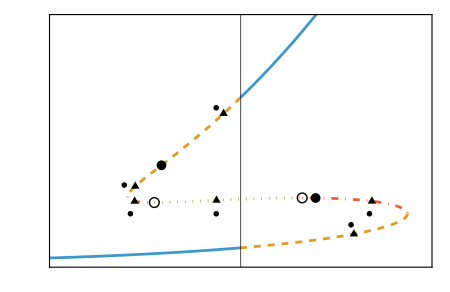

```mathematica
plot1=Show[ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHlist[[1]],ψHc1/.Tcritical},Axes->False,Frame->True,BaseStyle->texStyle,RotateLabel->False,FrameLabel->MaTeX[{"T/T_c","s/T_c^3"},Magnification->1.4],ImageSize->450,PlotStyle->Automatic,GridLines->{{1}/.Tcritical,None},AspectRatio->0.65,GridLinesStyle->Directive[Black],PlotRange->{{(*TofψH[ψHlist[[1]]]/TofψH[ψHc1]*)0.7,1.3},{0,110}},FrameTicks->{{yticks,None},{xticks,None}}],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHc2/.Tcritical,ψHlist[[-1]]},PlotRange->All],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHc1/.Tcritical,ψHt1/.turnings},PlotStyle->{ColorData[97][2],Dashed},PlotRange->All],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHt2/.turnings,ψHc2/.Tcritical},PlotStyle->{ColorData[97][2],Dashed},PlotRange->All],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHt1/.turnings,ψHt1/.turningsStability},PlotStyle->{ColorData[97][4],DotDashed},PlotRange->All],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHt2/.turningsStability,ψHt2/.turnings},PlotStyle->{ColorData[97][4],DotDashed},PlotRange->All],ParametricPlot[{TofψH[ψH]/TofψH[ψHc1],sofψH[ψH]/TofψH[ψHc1]^3}/.Tcritical,{ψH,ψHt1/.turningsStability,ψHt2/.turningsStability},PlotStyle->{ColorData[97][3],Dotted},PlotRange->All],ListPlot[{TofψH[#]/TofψH[ψHc1],sofψH[#]/TofψH[ψHc1]^3}/.Tcritical&/@ψHColl,PlotMarkers->{"●",10},PlotStyle->Black],ListPlot[{TofψH[#]/TofψH[ψHc1],sofψH[#]/TofψH[ψHc1]^3}/.Tcritical&/@{ψHt1/.turningsStability,ψHt2/.turningsStability},PlotMarkers->{"○",10},PlotStyle->Black],ListPlot[{TofψH[#]/TofψH[ψHc1],sofψH[#]/TofψH[ψHc1]^3}/.Tcritical&/@ψHRelevantBackgrounds,PlotStyle->{Black,PointSize[0.0001]},PlotMarkers->{(*"□"*)"▲",10}],Graphics[{Text[MaTeX["1",Magnification->1.2],{0.96,70}],Text[MaTeX["2",Magnification->1.2],{0.81,35}],Text[MaTeX["3",Magnification->1.2],{0.82,22}],Text[MaTeX["4",Magnification->1.2],{0.96,22}],Text[MaTeX["5",Magnification->1.2],{1.21,22}],Text[MaTeX["6",Magnification->1.2],{1.18,17}]}]]
```

```mathematica
xticks=Table[{x,MaTeX[ToString@NumberForm[x,{3,1}],Magnification->1.4]},{x,0.6,1.8,0.2}];
yticks=Table[{x,MaTeX[ToString@NumberForm[x,{3,1}],Magnification->1.4]},{x,0.7,1.3,0.1}];
```

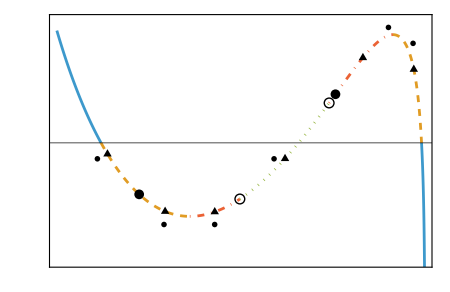

```mathematica
plot1=Show[ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHlist[[1]],ψHc1/.Tcritical},Axes->False,Frame->True,BaseStyle->texStyle,RotateLabel->False,FrameLabel->MaTeX[{"\\psi_H","T/T_c"},Magnification->1.4],ImageSize->450,PlotStyle->Automatic,GridLines->{None,{1}/.Tcritical},AspectRatio->0.65,GridLinesStyle->Directive[Black],PlotRange->{All,{0.7,1.31}},FrameTicks->{{yticks,None},{xticks,None}}],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHc2/.Tcritical,ψHlist[[-1]]},PlotRange->All],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHc1/.Tcritical,ψHt1/.turnings},PlotStyle->{ColorData[97][2],Dashed},PlotRange->All],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHt2/.turnings,ψHc2/.Tcritical},PlotStyle->{ColorData[97][2],Dashed},PlotRange->All],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHt1/.turnings,ψHt1/.turningsStability},PlotStyle->{ColorData[97][4],DotDashed},PlotRange->All],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHt2/.turningsStability,ψHt2/.turnings},PlotStyle->{ColorData[97][4],DotDashed},PlotRange->All],ParametricPlot[{ψH,TofψH[ψH]/TofψH[ψHc1]}/.Tcritical,{ψH,ψHt1/.turningsStability,ψHt2/.turningsStability},PlotStyle->{ColorData[97][3],Dotted},PlotRange->All],ListPlot[{#,TofψH[#]/TofψH[ψHc1]}/.Tcritical&/@ψHColl,PlotMarkers->{"●",10},PlotStyle->Black],ListPlot[{#,TofψH[#]/TofψH[ψHc1]}/.Tcritical&/@{ψHt1/.turningsStability,ψHt2/.turningsStability},PlotMarkers->{"○",10},PlotStyle->Black],ListPlot[{#,TofψH[#]/TofψH[ψHc1]}/.Tcritical&/@ψHRelevantBackgrounds,PlotStyle->{Black,PointSize[0.0001]},PlotMarkers->{(*"□"*)"▲",10}],Graphics[{Text[MaTeX["1",Magnification->1.2],{0.64,0.96}],Text[MaTeX["2",Magnification->1.2],{0.87,0.795}],Text[MaTeX["3",Magnification->1.2],{1.045,0.795}],Text[MaTeX["4",Magnification->1.2],{1.25,0.96}],Text[MaTeX["5",Magnification->1.2],{1.645,1.29}],Text[MaTeX["6",Magnification->1.2],{1.73,1.25}]}]]
```

### Save background data

```mathematica
Export[backgroundFile, {fields, thermo, constants, ℰH, ℰL, Tc, ψHlist}]
```

./background_data/phiM=0.8_phiQ=10._a=0._N_40_200_backgrounds.m

## 2. QNMs at q = 0 and the two relevant gapped modes

### Load backgrounds (from the file just saved)

```mathematica
{fields, thermo, constants, ℰH, ℰL, 
   Tc, ψHlist} = 
  Import["./background_data/phiM=0.8_phiQ=10._a=0._N_40_200_\
backgrounds.m"];

VV[ϕ_] := -3 - (3 ϕ^2)/2 - ϕ^4/3 - (
   4 𝒶^2 ϕ^16)/3 + 
   2/3 ϕ^12 (𝒶 (1/ϕM^2 + 72/ϕQ) - 
      2/ϕQ^2) + ϕ^6 (1/(2 ϕM^4) - 1/(3 ϕM^2) - 
      2/ϕQ) + (
   8 𝒶 ϕ^14 (-1 + 12 𝒶 ϕQ))/(
   3 ϕQ) + ϕ^8 (-4 𝒶 - (
      72 ϕM^2 - 16 ϕM^4 + ϕQ)/(
      12 ϕM^4 ϕQ)) + ϕ^10 (𝒶 (4/3 - 
         8/ϕM^2) + (2 (27 + ϕQ/ϕM^2))/(
      3 ϕQ^2)) /. constants
𝓌Hydro[q_, cs2_, 
  TΓ_] := (Sqrt[cs2] q - I π TΓ q^2)
DψH = 
  Cheb[ψHlist[[1]], ψHlist[[-1]], Length[ψHlist], 
    100][[2]];

DψHFD = NDSolve`FiniteDifferenceDerivative[1, ψHlist, "DifferenceOrder" -> 8]["DifferentiationMatrix"];
cs2FromE = DψHFD . (thermo[[;; , 6]]/thermo[[;; , 3]]^4)/
  DψHFD . (thermo[[;; , 5]]/thermo[[;; , 3]]^4); 
cs2 = (DψHFD . Log[thermo[[All, 1]]/thermo[[All, 3]]])/(DψHFD . 
     Log[thermo[[All, 2]]/thermo[[All, 3]]^3]);
ζovers = 
  1/π (DψHFD . (Log[thermo[[;; , 2]]/thermo[[;; , 3]]^3]))^-2;
TΓs = (1/(3 π) + ζovers);
idCrit = Position[cs2, Min[cs2]][[1, 1]];
Nbackgrounds = Length[ψHlist];
Print["\!\(\*SubscriptBox[\(N\), \(backgrounds\)]\) = " <> 
  ToString[Nbackgrounds] ]
constants
```

N_backgrounds = 200

{κ→1,ϕM→4/5,ϕQ→10,𝒶→0}

```mathematica
(*This is the desired precision for QNMs. Running times scale fast with it.*)
prec = (*MachinePrecision*)30;
Nu=Dimensions[fields][[3]]
u=SetPrecision[Reverse[Table[1/2+1/2 Cos[((j-1) π)/(Nu-1)],{j,1,Nu}]],prec];
Du = NDSolve`FiniteDifferenceDerivative[1, u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
Du2 = NDSolve`FiniteDifferenceDerivative[2,u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
grid = {u,Du,Du2};
u = grid[[1]];
u//Precision
```

40

27.2078

Get turning and instability switch points (if there are any)

```mathematica
TofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 1]]/thermo[[All, 3]]}]];
sofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 2]]/thermo[[All, 3]]^3}]];
turning1 = FindRoot[TofψH'[ψHt1], {ψHt1, ψHturningGuess[[1]]}];
turning2 = FindRoot[TofψH'[ψHt2], {ψHt2, ψHturningGuess[[2]]}];
turnings = Join[turning1, turning2];
If[stabilitySwitch,
  turningStability1 = FindRoot[sofψH'[ψHt1], {ψHt1, ψHstabilityGuess[[1]]}];
  turningStability2 = FindRoot[sofψH'[ψHt2], {ψHt2, ψHstabilityGuess[[2]]}];
  turningsStability = Join[turningStability1, turningStability2]];
Clear[turning1, turning2, turningStability1, turningStability2];
```

```mathematica
idTurning1 = Length[Select[ψHlist, # < (ψHt1 /. turnings) &]];
idTurning2 = Length[Select[ψHlist, # <= (ψHt2 /. turnings) &]] + 1;
{idTurning1, idTurning2}

idInstability1 = Length[Select[ψHlist, # < (ψHt1 /. turningsStability) &]];
idInstability2 = Length[Select[ψHlist, # <= (ψHt2 /. turningsStability) &]] + 1;
{idInstability1, idInstability2}
```

{82,163}

{100,133}

Plot of c_s^2 and viscosities check

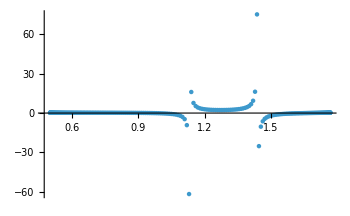
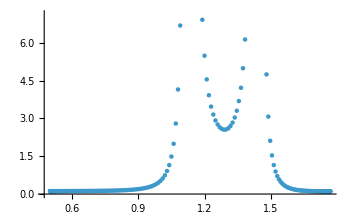

```mathematica
Row[{ListPlot[{Transpose[{ψHlist,cs2}]},ImageSize->350,PlotRange->All],ListPlot[Transpose[{ψHlist,TΓs}],ImageSize->350]}]
```

### All gapped modes at q = 0 (parallel)

```mathematica
numberProcessors = 10;
If[$KernelCount == 0, LaunchKernels[numberProcessors]];
```

```mathematica
q = 0;
```

```mathematica
NQNMs=0;eigenfunctions=False;
ImωgappedCutoff = 10;
tol=10^-5;
gappedModes={};
solnumber=0;
SetSharedVariable[grid,fields,q,prec,NQNMs,eigenfunctions,gappedModes,solnumber];
Monitor[ParallelDo[
T = thermo[[n,1]];
(*Track the conjugate pairs*)
QNM1 =GetQNM[grid,fields[[n]],VV,q,T,prec,NQNMs,eigenfunctions];
AppendTo[gappedModes,{n,Select[QNM1,Abs[Im[#]]<=ImωgappedCutoff&&#!=∞&&#!=0&&Abs[Im[#]]>=tol&]}];
solnumber+=1;
,{n,1,Nbackgrounds},Method->"CoarsestGrained"];,{solnumber,gappedModes[[-1]]}];//AbsoluteTiming
```

{359.178,Null}

```mathematica
gappedModesAux = gappedModes;
gappedModes=Sort[gappedModesAux][[;;,2]];
```

### Tracking the two relevant gapped modes

```mathematica
(* ---- Seed for tracking the two relevant gapped modes at q = 0 ---- *)
ψHseed = 0.925; SelectModes = {-0.48 I, -3.44 I};
```

```mathematica
id = First[Ordering[Abs[ψHlist - ψHseed], 1]];
pairofModes = (gappedModes[[id]][[#]] &) /@ ((Position[Abs[gappedModes[[id]] - #], Min[Abs[gappedModes[[id]] - #]]] &) /@ SelectModes)[[All, 1, 1]];
{ψHlist[[id]], pairofModes}
```

{0.923583965486101690006940668490154785265502012507355377984383566908846222847621577411429445864665754,{-5.149×10^-27-0.498576474408163535525487251546 ⅈ,0.-3.48059241879775118725521510637 ⅈ}}

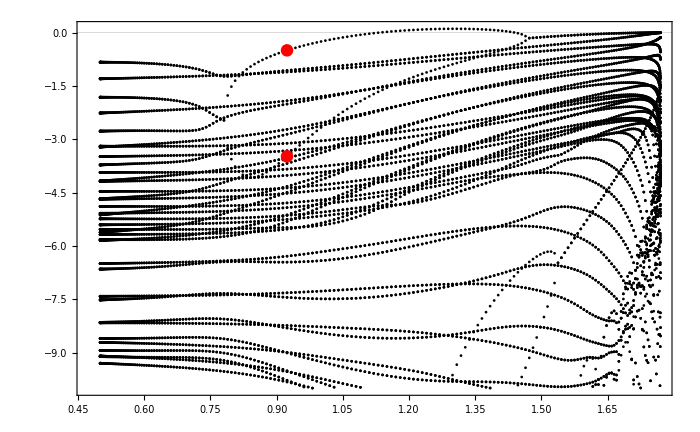

```mathematica
Show[ListPlot[Table[Table[{ψHlist[[n]],Im@gappedModes[[n,m]]},{m,1,Length[gappedModes[[n,;;]]]}],{n,1,Nbackgrounds}],Frame->True,GridLines->{None,{0}},ImageSize->700,PlotStyle->Black],ListPlot[{{ψHlist[[id]],Im@pairofModes[[1]]},{ψHlist[[id]],Im@pairofModes[[2]]}},PlotStyle->Red]]
```

```mathematica
TrackLightMode={pairofModes[[2]]};
TrackLightModeC={pairofModes[[1]]};
(gappedModes[[id,#]]&/@Position[Abs[gappedModes[[id,;;]]-TrackLightMode[[-1]]],Min[Abs[gappedModes[[id,;;]]-TrackLightMode[[-1]]]]][[1]])[[1]]
(gappedModes[[id,#]]&/@Position[Abs[gappedModes[[id,;;]]-TrackLightModeC[[-1]]],Min[Abs[gappedModes[[id,;;]]-TrackLightModeC[[-1]]]]][[1]])[[1]]
```

0.-3.48059241879775118725521510637 ⅈ

-5.149×10^-27-0.498576474408163535525487251546 ⅈ

```mathematica
(*Light mode*)
Do[
AppendTo[TrackLightMode,(gappedModes[[n,#]]&/@Position[Abs[gappedModes[[n,;;]]-TrackLightMode[[-1]]],Min[Abs[gappedModes[[n,;;]]-TrackLightMode[[-1]]]]][[1]])[[1]]]
,{n,id-1,1,-1}];
TrackLightMode=Reverse[TrackLightMode];
Do[
AppendTo[TrackLightMode,(gappedModes[[n,#]]&/@Position[Abs[gappedModes[[n,;;]]-TrackLightMode[[-1]]],Min[Abs[gappedModes[[n,;;]]-TrackLightMode[[-1]]]]][[1]])[[1]]]
,{n,id+1,Nbackgrounds}];
(*Conjugate mode*)
Do[
AppendTo[TrackLightModeC,(gappedModes[[n,#]]&/@Position[Abs[gappedModes[[n,;;]]-TrackLightModeC[[-1]]],Min[Abs[gappedModes[[n,;;]]-TrackLightModeC[[-1]]]]][[1]])[[1]]]
,{n,id-1,1,-1}];
TrackLightModeC=Reverse[TrackLightModeC];
Do[
AppendTo[TrackLightModeC,(gappedModes[[n,#]]&/@Position[Abs[gappedModes[[n,;;]]-TrackLightModeC[[-1]]],Min[Abs[gappedModes[[n,;;]]-TrackLightModeC[[-1]]]]][[1]])[[1]]]
,{n,id+1,Nbackgrounds}];
```

```mathematica
{LightMode1, LightMode2} = {TrackLightMode, TrackLightModeC};
```

### Plot: relevant gapped modes as a function of ψH

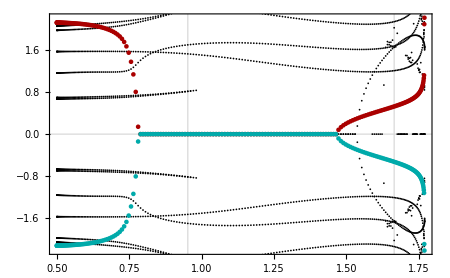
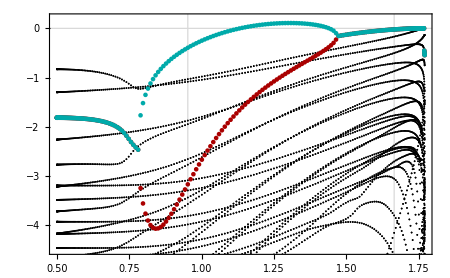

```mathematica
nfinal = Nbackgrounds;
Row[{plot1=Show[ListPlot[Table[Table[{ψHlist[[n]],Re@gappedModes[[n,m]]},{m,1,Length[gappedModes[[n,;;]]]}],{n,1,nfinal}],PlotStyle->Black,Frame->True,GridLines->{{ψHlist[[idTurning1]],ψHlist[[idTurning2]]},{0}},GridLinesStyle->Thickness[0.002],ImageSize->450,PlotRange->{ψHlist[[{1,-1}]],{-2.2,2.2}},BaseStyle->texStyle,FrameLabel->MaTeX[{"\\psi_H","\\Re\\omega/\\left(2\\pi T\\right)"},Magnification->1.4]],ListPlot[{Transpose[{ψHlist,Abs[Re[TrackLightMode]]}],Transpose[{ψHlist,-Abs[Re[TrackLightModeC]]}]},PlotStyle->{Darker@Red,Darker@Cyan}]],plot2=Show[ListPlot[Table[Table[{ψHlist[[n]],Im@gappedModes[[n,m]]},{m,1,Length[gappedModes[[n,;;]]]}],{n,1,nfinal}],PlotStyle->Black,Frame->True,GridLines->{{ψHlist[[idTurning1]],ψHlist[[idTurning2]]},{0}},GridLinesStyle->Thickness[0.002],ImageSize->450,PlotRange->{ψHlist[[{1,-1}]],{-4.5,0.2}},BaseStyle->texStyle,FrameLabel->MaTeX[{"\\psi_H","\\Im\\omega/\\left(2\\pi T\\right)"},Magnification->1.4]],ListPlot[{Transpose[{ψHlist,Im[TrackLightMode]}],Transpose[{ψHlist,Im[TrackLightModeC]}]},PlotStyle->{Darker@Red,Darker@Cyan}]]}]
```

```mathematica
(*Export[figsDir <> "gapped_Re_vs_psiH_" <> tag <> ".pdf", plot1, ImageResolution -> 300];
Export[figsDir <> "gapped_Im_vs_psiH_" <> tag <> ".pdf", plot2, ImageResolution -> 300];*)
```

Export the gapped mode data at q=0

```mathematica
Export["./QNM_data/datawgapped"<>"_phiM="<>ToString[ϕM/.constants//N]<>"_phiQ="<>ToString[ϕQ/.constants//N]<>"_Nz_"<>ToString[Nu]<>"_.m",{TrackLightMode,TrackLightModeC}]
```

./datawgapped_phiM=0.8_phiQ=10._Nz_40_.m

```mathematica
Export["./QNM_data/datawALLgapped"<>"_phiM="<>ToString[ϕM/.constants//N]<>"_phiQ="<>ToString[ϕQ/.constants//N]<>"_Nz_"<>ToString[Nu]<>"_.m",gappedModes]
```

./datawALLgapped_phiM=0.8_phiQ=10._Nz_40_.m

## 3. Sound and gapped modes as a function of small q

### Load backgrounds

```mathematica
{fields, thermo, constants, ℰH, ℰL, 
   Tc, ψHlist} = 
  Import["./background_data/phiM=0.8_phiQ=10._a=0._N_40_200_\
backgrounds.m"];

VV[ϕ_] := -3 - (3 ϕ^2)/2 - ϕ^4/3 - (
   4 𝒶^2 ϕ^16)/3 + 
   2/3 ϕ^12 (𝒶 (1/ϕM^2 + 72/ϕQ) - 
      2/ϕQ^2) + ϕ^6 (1/(2 ϕM^4) - 1/(3 ϕM^2) - 
      2/ϕQ) + (
   8 𝒶 ϕ^14 (-1 + 12 𝒶 ϕQ))/(
   3 ϕQ) + ϕ^8 (-4 𝒶 - (
      72 ϕM^2 - 16 ϕM^4 + ϕQ)/(
      12 ϕM^4 ϕQ)) + ϕ^10 (𝒶 (4/3 - 
         8/ϕM^2) + (2 (27 + ϕQ/ϕM^2))/(
      3 ϕQ^2)) /. constants
𝓌Hydro[q_, cs2_, 
  TΓ_] := (Sqrt[cs2] q - I π TΓ q^2)
DψH = 
  Cheb[ψHlist[[1]], ψHlist[[-1]], Length[ψHlist], 
    100][[2]];

DψHFD = NDSolve`FiniteDifferenceDerivative[1, ψHlist, "DifferenceOrder" -> 8]["DifferentiationMatrix"];
cs2FromE = DψHFD . (thermo[[;; , 6]]/thermo[[;; , 3]]^4)/
  DψHFD . (thermo[[;; , 5]]/thermo[[;; , 3]]^4); 
cs2 = (DψHFD . Log[thermo[[All, 1]]/thermo[[All, 3]]])/(DψHFD . 
     Log[thermo[[All, 2]]/thermo[[All, 3]]^3]);
ζovers = 
  1/π (DψHFD . (Log[thermo[[;; , 2]]/thermo[[;; , 3]]^3]))^-2;
TΓs = (1/(3 π) + ζovers);
idCrit = Position[cs2, Min[cs2]][[1, 1]];
Nbackgrounds = Length[ψHlist];
Print["\!\(\*SubscriptBox[\(N\), \(backgrounds\)]\) = " <> 
  ToString[Nbackgrounds] ]
constants
```

N_backgrounds = 200

{κ→1,ϕM→4/5,ϕQ→10,𝒶→0}

```mathematica
(*This is the desired precision for QNMs. Running times scale fast with it.*)
prec =30;
Nu=Dimensions[fields][[3]]
u=SetPrecision[Reverse[Table[1/2+1/2 Cos[((j-1) π)/(Nu-1)],{j,1,Nu}]],prec];
Du = NDSolve`FiniteDifferenceDerivative[1, u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
Du2 = NDSolve`FiniteDifferenceDerivative[2,u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
grid = {u,Du,Du2};
u = grid[[1]];
u//Precision
```

40

27.2078

Get turning and instability switch points (if there are any)

```mathematica
TofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 1]]/thermo[[All, 3]]}]];
sofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 2]]/thermo[[All, 3]]^3}]];
turning1 = FindRoot[TofψH'[ψHt1], {ψHt1, ψHturningGuess[[1]]}];
turning2 = FindRoot[TofψH'[ψHt2], {ψHt2, ψHturningGuess[[2]]}];
turnings = Join[turning1, turning2];
If[stabilitySwitch,
  turningStability1 = FindRoot[sofψH'[ψHt1], {ψHt1, ψHstabilityGuess[[1]]}];
  turningStability2 = FindRoot[sofψH'[ψHt2], {ψHt2, ψHstabilityGuess[[2]]}];
  turningsStability = Join[turningStability1, turningStability2]];
Clear[turning1, turning2, turningStability1, turningStability2];
```

```mathematica
idTurning1 = Length[Select[ψHlist, # < (ψHt1 /. turnings) &]];
idTurning2 = Length[Select[ψHlist, # <= (ψHt2 /. turnings) &]] + 1;
{idTurning1, idTurning2}

idInstability1 = Length[Select[ψHlist, # < (ψHt1 /. turningsStability) &]];
idInstability2 = Length[Select[ψHlist, # <= (ψHt2 /. turningsStability) &]] + 1;
{idInstability1, idInstability2}
```

{82,163}

{100,133}

Plot of c_s^2 and viscosities check

```mathematica
Row[{ListPlot[{Transpose[{ψHlist,cs2}]},ImageSize->350,PlotRange->All],ListPlot[Transpose[{ψHlist,TΓs}],ImageSize->350]}]
```

-Graphics--Graphics-

### Compute finite q QNM for sound and relevant gapped modes

Load the q=0 data for the relevant gapped modes

```mathematica
{LightMode1,LightMode2}=Import["./QNM_data/datawgapped_phiM=0.8_phiQ=10._Nz_40_.m"];
```

```mathematica
Nq=10;
{nmin,nmax} = {-6,-1};
qlist =1/(2 π) 10^Range[nmin,nmax,(nmax-nmin)/(Nq-1)];
2 π qlist//N//Log10
{qmin,qmax} = qlist[[{1,-1}]];
```

{-6.,-5.44444,-4.88889,-4.33333,-3.77778,-3.22222,-2.66667,-2.11111,-1.55556,-1.}

```mathematica
numberProcessors = 10;
If[$KernelCount == 0, LaunchKernels[numberProcessors]];
```

```mathematica
qlist = 1/(2 π) 10^Range[nmin, nmax, (nmax - nmin)/(Nq - 1)];
Log10[N[2 π qlist]]
{qmin, qmax} = qlist[[{1, -1}]];
UnsetShared[q];
```

{-6.,-5.44444,-4.88889,-4.33333,-3.77778,-3.22222,-2.66667,-2.11111,-1.55556,-1.}

```mathematica
{NminQNMs,NmaxQNMs}={1,Nbackgrounds};
NQNMs=0;eigenfunctions=False;
soundModeAll1={};soundModeAll2={};
gappedModeAll1={};gappedModeAll2={};
SetSharedVariable[qlist,prec,NQNMs,eigenfunctions,soundMode1,soundMode2,gappedMode1,gappedMode2,solnumber];
Monitor[Do[
soundMode1={};soundMode2={};gappedMode1 = {};gappedMode2={};
solnumber=0;
ParallelDo[
q = qlist[[n]];
(*Track the conjugate pairs*)
mode1 = 𝓌Hydro[q,cs2[[m]],TΓ[[m]]];
mode2 = 𝓌Hydro[-q,cs2[[m]],TΓ[[m]]];

QNM1 =GetQNM[grid,fields[[m]],VV,q,thermo[[m,1]],prec,NQNMs,eigenfunctions];

AppendTo[soundMode1,{q, QNM1[[Position[QNM1-mode1//Abs,QNM1-mode1//Abs//Min][[1,1]]]]}];
AppendTo[soundMode2,{q, QNM1[[Position[QNM1-mode2//Abs,QNM1-mode2//Abs//Min][[1,1]]]]}];
AppendTo[gappedMode1,{q, QNM1[[Position[Abs[QNM1-LightMode1[[m]]],Min[Abs[QNM1-LightMode1[[m]]]]][[1,1]]]]}];
AppendTo[gappedMode2,{q, QNM1[[Position[Abs[QNM1-LightMode2[[m]]],Min[Abs[QNM1-LightMode2[[m]]]]][[1,1]]]]}];
solnumber+=1;
,{n,1,Nq},Method->"CoarsestGrained"];
soundMode1Aux=Sort[SetPrecision[soundMode1,prec]][[;;,2]];
soundMode2Aux=Sort[SetPrecision[soundMode2,prec]][[;;,2]];
gappedMode1Aux=Sort[SetPrecision[gappedMode1,prec]][[;;,2]];
gappedMode2Aux=Sort[SetPrecision[gappedMode2,prec]][[;;,2]];

AppendTo[soundModeAll1,soundMode1Aux];
AppendTo[soundModeAll2,soundMode2Aux];
AppendTo[gappedModeAll1,gappedMode1Aux];
AppendTo[gappedModeAll2,gappedMode2Aux];
,{m,NminQNMs,NmaxQNMs}],{m,solnumber,soundMode1[[-1]],soundMode2[[-1]],gappedMode1[[-1]],gappedMode2[[-1]]}];//AbsoluteTiming
Clear[soundMode1Aux,soundMode2Aux,gappedMode1Aux,gappedMode2Aux,soundMode1,soundMode2,gappedMode1,gappedMode2]
```

{12061.9,Null}

### Save QNM data

```mathematica
Export["./QNM_data/datawofq-sound-gapped-"<>"_phiM="<>ToString[ϕM/.constants//N]<>"_phiQ="<>ToString[ϕQ/.constants//N]<>"_Nz_"<>ToString[Nu]<>".m",{soundModeAll1,soundModeAll2,gappedModeAll1,gappedModeAll2}];
```

### Plots: sound and gapped modes vs q for some background

Top row: the two sound modes against the hydrodynamic dispersion relation Hydro. Bottom row: the two gapped modes against their q = 0 value.

ψH = 1.77   (background 200)

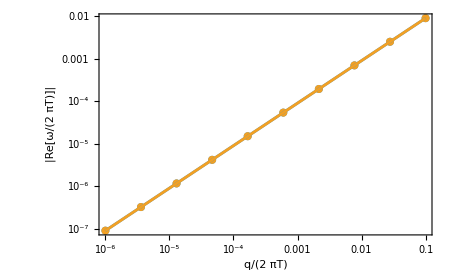
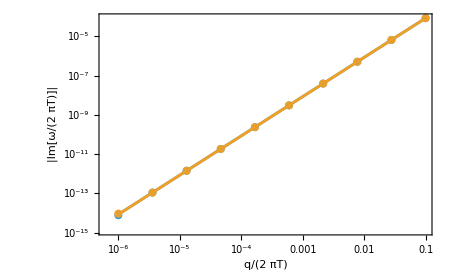

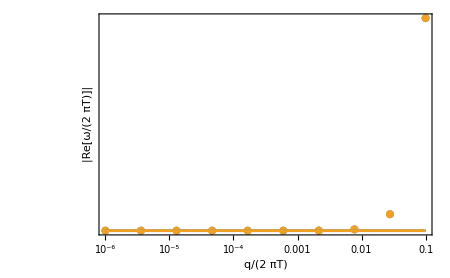
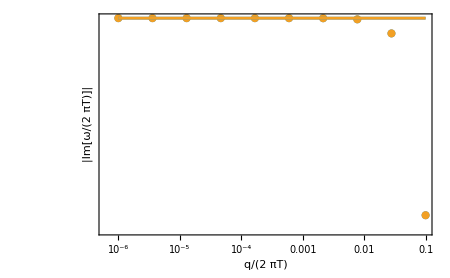

```mathematica
number = Nbackgrounds;

Print[Style[Row[{"ψH = ", N[ψHlist[[number]]], "   (background ", number, ")"}], Bold, 14]];
 Print[Row[{Show[ListLogLogPlot[{Transpose[{Abs[2*Pi*qlist], Abs[Re[soundModeAll1[[number, 1 ;; All]]]]}], Transpose[{Abs[2*Pi*qlist], Abs[Re[soundModeAll2[[number, 1 ;; All]]]]}]},
       Frame -> True, FrameLabel -> {"\!\(\*FractionBox[\(q\), \(2  πT\)]\)", "|Re[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]|"}, ImageSize -> 450],
      LogLogPlot[{Abs[Re[Sqrt[cs2[[number]]]*(q/(2*Pi)) - I*Pi*TΓ[[number]]*(q/(2*Pi))^2]], Abs[Re[(-Sqrt[cs2[[number]]])*(q/(2*Pi)) - I*Pi*TΓ[[number]]*(q/(2*Pi))^2]]},
       {q, 2*Pi*Abs[qmin], 2*Pi*Abs[qmax]}], PlotRange -> All],
     Show[ListLogLogPlot[{Transpose[{Abs[2*Pi*qlist], Abs[Im[soundModeAll1[[number, 1 ;; All]]]]}], Transpose[{Abs[2*Pi*qlist], Abs[Im[soundModeAll2[[number, 1 ;; All]]]]}]},
       Frame -> True, FrameLabel -> {"\!\(\*FractionBox[\(q\), \(2  πT\)]\)", "|Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]|"}, ImageSize -> 450],
      LogLogPlot[{Abs[Im[Sqrt[cs2[[number]]]*(q/(2*Pi)) - I*Pi*TΓ[[number]]*(q/(2*Pi))^2]], Abs[Im[(-Sqrt[cs2[[number]]])*(q/(2*Pi)) - I*Pi*TΓ[[number]]*(q/(2*Pi))^2]]},
       {q, 2*Pi*Abs[qmin], 2*Pi*Abs[qmax]}]]}]];
 Print[Row[{Show[ListLogLogPlot[{Transpose[{Abs[2*Pi*qlist], Abs[Re[gappedModeAll1[[number, 1 ;; All]]]]}], Transpose[{Abs[2*Pi*qlist], Abs[Re[gappedModeAll2[[number, 1 ;; All]]]]}]},
       Frame -> True, FrameLabel -> {"\!\(\*FractionBox[\(q\), \(2  πT\)]\)", "|Re[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]|"}, ImageSize -> 450],
      LogLogPlot[{Abs[Re[LightMode1[[number]]]], Abs[Re[LightMode2[[number]]]]}, {q, 2*Pi*Abs[qmin], 2*Pi*Abs[qmax]}], PlotRange -> All],
     Show[ListLogLogPlot[{Transpose[{Abs[2*Pi*qlist], Abs[Im[gappedModeAll1[[number, 1 ;; All]]]]}], Transpose[{Abs[2*Pi*qlist], Abs[Im[gappedModeAll2[[number, 1 ;; All]]]]}]},
       Frame -> True, FrameLabel -> {"\!\(\*FractionBox[\(q\), \(2  πT\)]\)", "|Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]|"}, ImageSize -> 450],
      LogLogPlot[{Abs[Im[LightMode1[[number]]]], Abs[Im[LightMode2[[number]]]]}, {q, 2*Pi*Abs[qmin], 2*Pi*Abs[qmax]}]]}]]

Clear[number]
```

## 4. Extract EFT parameters

This section takes all previously generated data, loads it, and extracts from it the parameter combinations required for the EFT

### Load backgrounds

```mathematica
{fields, thermo, constants, ℰH, ℰL, 
   Tc, ψHlist} = 
  Import["./background_data/phiM=0.8_phiQ=10._a=0._N_40_200_\
backgrounds.m"];

VV[ϕ_] := -3 - (3 ϕ^2)/2 - ϕ^4/3 - (
   4 𝒶^2 ϕ^16)/3 + 
   2/3 ϕ^12 (𝒶 (1/ϕM^2 + 72/ϕQ) - 
      2/ϕQ^2) + ϕ^6 (1/(2 ϕM^4) - 1/(3 ϕM^2) - 
      2/ϕQ) + (
   8 𝒶 ϕ^14 (-1 + 12 𝒶 ϕQ))/(
   3 ϕQ) + ϕ^8 (-4 𝒶 - (
      72 ϕM^2 - 16 ϕM^4 + ϕQ)/(
      12 ϕM^4 ϕQ)) + ϕ^10 (𝒶 (4/3 - 
         8/ϕM^2) + (2 (27 + ϕQ/ϕM^2))/(
      3 ϕQ^2)) /. constants
𝓌Hydro[q_, cs2_, 
  TΓ_] := (Sqrt[cs2] q - I π TΓ q^2)
DψH = 
  Cheb[ψHlist[[1]], ψHlist[[-1]], Length[ψHlist], 
    100][[2]];

(* local 8th-order finite-difference d/dψH (9-point stencil on ψHlist), used for all thermodynamic derivatives: the global spectral DψH is off by ~1e-4 in d log s/dψH, which near the poles of c_s^2 makes c_s^2 and ζ/s noisy *)
DψHFD = NDSolve`FiniteDifferenceDerivative[1, ψHlist, "DifferenceOrder" -> 8]["DifferentiationMatrix"];
cs2FromE = DψHFD . (thermo[[;; , 6]]/thermo[[;; , 3]]^4)/
  DψHFD . (thermo[[;; , 5]]/thermo[[;; , 3]]^4); 
cs2 = (DψHFD . Log[thermo[[All, 1]]/thermo[[All, 3]]])/(DψHFD . 
     Log[thermo[[All, 2]]/thermo[[All, 3]]^3]);
ζovers = 
  1/π (DψHFD . (Log[thermo[[;; , 2]]/thermo[[;; , 3]]^3]))^-2;
TΓs = (1/(3 π) + ζovers);
idCrit = Position[cs2, Min[cs2]][[1, 1]];
Nbackgrounds = Length[ψHlist];
Print["\!\(\*SubscriptBox[\(N\), \(backgrounds\)]\) = " <> 
  ToString[Nbackgrounds] ]
constants
```

N_backgrounds = 200

{κ→1,ϕM→4/5,ϕQ→10,𝒶→0}

```mathematica
(*This is the desired precision for QNMs. Running times scale fast with it.*)
prec =30;
Nu=Dimensions[fields][[3]]
u=SetPrecision[Reverse[Table[1/2+1/2 Cos[((j-1) π)/(Nu-1)],{j,1,Nu}]],prec];
Du = NDSolve`FiniteDifferenceDerivative[1, u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
Du2 = NDSolve`FiniteDifferenceDerivative[2,u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
grid = {u,Du,Du2};
u = grid[[1]];
u//Precision
```

40

27.2078

Get turning and instability switch points (if there are any)

```mathematica
TofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 1]]/thermo[[All, 3]]}]];
sofψH = Interpolation[Transpose[{ψHlist, thermo[[All, 2]]/thermo[[All, 3]]^3}]];
turning1 = FindRoot[TofψH'[ψHt1], {ψHt1, ψHturningGuess[[1]]}];
turning2 = FindRoot[TofψH'[ψHt2], {ψHt2, ψHturningGuess[[2]]}];
turnings = Join[turning1, turning2];
If[stabilitySwitch,
  turningStability1 = FindRoot[sofψH'[ψHt1], {ψHt1, ψHstabilityGuess[[1]]}];
  turningStability2 = FindRoot[sofψH'[ψHt2], {ψHt2, ψHstabilityGuess[[2]]}];
  turningsStability = Join[turningStability1, turningStability2]];
Clear[turning1, turning2, turningStability1, turningStability2];
```

```mathematica
idTurning1 = Length[Select[ψHlist, # < (ψHt1 /. turnings) &]];
idTurning2 = Length[Select[ψHlist, # <= (ψHt2 /. turnings) &]] + 1;
{idTurning1, idTurning2}

idInstability1 = Length[Select[ψHlist, # < (ψHt1 /. turningsStability) &]];
idInstability2 = Length[Select[ψHlist, # <= (ψHt2 /. turningsStability) &]] + 1;
{idInstability1, idInstability2}
```

{82,163}

{100,133}

### Load QNM data

```mathematica
(*Load q=0 gapped mode data*)
{LightMode1,LightMode2}=Import["./QNM_data/datawgapped_phiM=0.8_phiQ=10._Nz_40_.m"];

(*Load low q data of gapped and sound modes*)
{soundModeAll1,soundModeAll2,gappedModeAll1,gappedModeAll2} = Import["./QNM_data/datawofq-sound-gapped-_phiM=0.8_phiQ=10._Nz_40.m"];
```

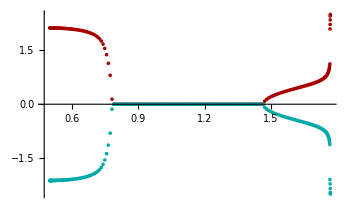
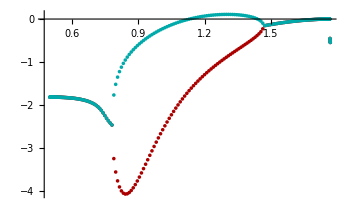

```mathematica
Row[{ListPlot[{Transpose[{ψHlist,Re[LightMode1]}],Transpose[{ψHlist,Re[LightMode2]}]},PlotStyle->{Darker@Red,Darker@Cyan},ImageSize->350],ListPlot[{Transpose[{ψHlist,Im[LightMode1]}],Transpose[{ψHlist,Im[LightMode2]}]},PlotStyle->{Darker@Red,Darker@Cyan},ImageSize->350]}]
```

```mathematica
Nq=10;
{nmin,nmax} = {-6,-1};
qlist =1/(2 π) 10^Range[nmin,nmax,(nmax-nmin)/(Nq-1)];
{qmin,qmax} = qlist[[{1,-1}]];
tol = 10^-7;
idColl1=Position[LightMode1,Select[LightMode1,Abs[Re[#]]<=tol&][[1]]][[1,1]];
idColl2=Position[LightMode1,Select[LightMode1,Abs[Re[#]]<=tol&][[-1]]][[1,1]];
{idColl1,idTurning1,idInstability1,idInstability2,idColl2,idTurning2}
```

{64,82,100,133,135,163}

```mathematica
(*Split the modes into two lists (useful for ListPlot)*)
{TrackLightMode,TrackLightModeC} = {LightMode1,LightMode2};
TrackLightMode = -Abs[Re[LightMode1]]+ⅈ Im[LightMode1];
TrackLightModeC = Abs[Re[LightMode2]]+ⅈ Im[LightMode2];
```

```mathematica
gridlines = ψHlist[[{idTurning1,idTurning2}]];
```

```mathematica
(*Row[{ListPlot[{Transpose[{ψHlist,Re[TrackLightMode]}],Transpose[{ψHlist,Re[TrackLightModeC]}]},PlotStyle->{Darker@Red,Darker@Cyan},ImageSize->350],ListPlot[{Transpose[{ψHlist,Im[TrackLightMode]}],Transpose[{ψHlist,Im[TrackLightModeC]}]},PlotStyle->{Darker@Red,Darker@Cyan},ImageSize->350]}]*)
```

Load and check q_max^2 (generated by code in zero_frequency folder)

```mathematica
(*Load the Subscript[q, max] data*)
q2List = Import["./dataqsquared_phiM_0.8_N60.m"];
q02Inter = Interpolation[q2List];

Nmin=Position[ψHlist-q2List[[1,1]],Select[ψHlist-q2List[[1,1]],#>=0&][[1]]][[1,1]];
Nmax=Position[ψHlist-q2List[[-1,1]],Select[ψHlist-q2List[[-1,1]],#<=0&][[-1]]][[1,1]];
```

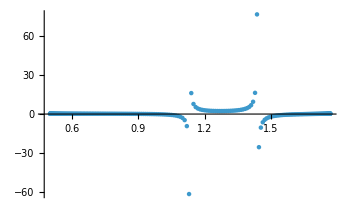
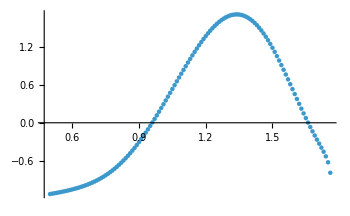

```mathematica
Row[{ListPlot[Transpose[{ψHlist,cs2}],ImageSize->350,PlotRange->All],ListPlot[q2List,ImageSize->350]}]
```

Plots of sound ω vs q

```mathematica
qlist[[1]]
```

1/(2000000 π)

```mathematica
qmin
```

1/(2000000 π)

```mathematica
nback =1;
If[idTurning1<=nback<=idInstability1||idInstability2<=nback<=idTurning2,{normRe,normIm} ={ 3,1},{normRe,normIm} ={1,2}];
```

```mathematica
cs2[[idTurning1+1]]
```

-0.008518988607161841416228917568835856439042312024733862566356342833389885265916176165260299872

Throw::nocatch: Uncaught Throw[Hold[Message[Rule::argr,Rule,2],False],iArgumentsMessage] returned to top level.

$Aborted[]

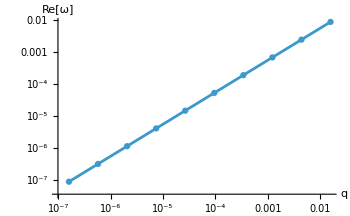
-Graphics-ListLogLogPlot[{{{1/(2000000 π),9.0739003462048001411438×10^-15},{1/(200000 10^(4/9) π),1.1696062256700887023213×10^-13},{1/(20000 10^(8/9) π),1.51054131658360468537171×10^-12},{1/(20000 10^(1/3) π),1.95094105848075004391472×10^-11},{1/(2000 10^(7/9) π),2.519737182800660012827252×10^-10},{1/(2000 10^(2/9) π),3.254365713097579147622858×10^-9},{1/(200 10^(2/3) π),4.203174915646992830408648×10^-8},{1/(200 10^(1/9) π),5.42860863940804785132281948×10^-7},{1/(20 10^(5/9) π),7.01130908068379936421445947×10^-6},{1/(20 π),0.00009055310598573554314745666623}}},ImageSize→350,AxesLabel→{q,Im[ω]},-Graphics-]

```mathematica
Row[{Show[ListLogLogPlot[{Transpose[{qlist,Abs[Re[soundModeAll1[[nback]]]]}]},ImageSize->350,AxesLabel->{"q","Re[ω]"}],LogLogPlot[Re[√cs2[[nback]]]q,{q,qmin,qmax}]],ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback]]]]}]},ImageSize->350,AxesLabel->{"q","Im[ω]"},LogLogPlot[Im[√cs2[[nback]]]q,{q,qmin,qmax}]]}]
```

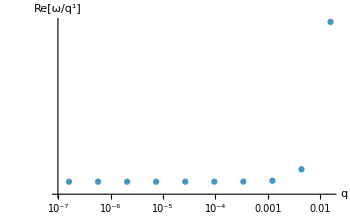
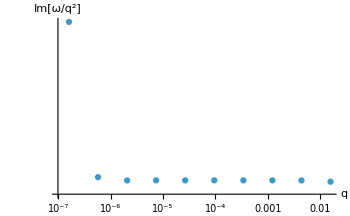

```mathematica
Row[{ListLogLogPlot[{Transpose[{qlist,Abs[Re[soundModeAll1[[nback]]]/qlist^normRe]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Re[ω/q^(`1`)]"][normRe]}],ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback]]]/qlist^normIm]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Im[ω/q^(`1`)]"][normIm]}]}]
```

### M_1 and M_2

```mathematica
EFTparameters={};
Do[
eq1=√(M2-(γ̃)^2)-Abs[Re[TrackLightMode[[n]]]];
eq2=-γ̃-Im[TrackLightMode[[n]]];
sol=NSolve[eq1==0 && eq2==0,{M2,γ̃}][[1]];
AppendTo[EFTparameters,{M2,γ̃}/.sol]
,{n,1,idColl1-1}];
Do[
mode1=√((γ̃)^2-M2)-γ̃;
mode2=-√((γ̃)^2-M2)-γ̃;
eq1 = mode1+mode2 - (Im[TrackLightMode[[n]]]+Im[TrackLightModeC[[n]]]);
eq2 = (mode1-mode2)^2 - (Im[TrackLightMode[[n]]]-Im[TrackLightModeC[[n]]])^2;
sol=NSolve[eq1==0 && eq2==0,{M2,γ̃}][[1]];
AppendTo[EFTparameters,{M2,γ̃}/.sol];
,{n,idColl1,idColl2}];
Do[
eq1=√(M2-(γ̃)^2)-Abs[Re[TrackLightMode[[n]]]];
eq2=-γ̃-Im[TrackLightMode[[n]]];
sol=NSolve[eq1==0 && eq2==0,{M2,γ̃}][[1]];
AppendTo[EFTparameters,{M2,γ̃}/.sol]
,{n,idColl2+1,Nbackgrounds}];
Clear[eq1,eq2,sol,mode1,mode2]

Clear[eq1,eq2,sol]
```

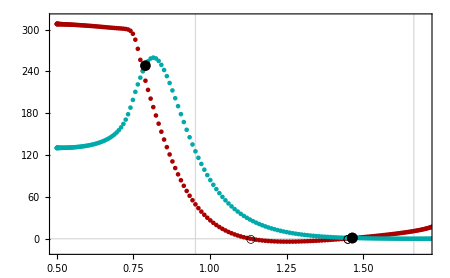

```mathematica
plot1=Show[ListPlot[{Transpose[{ψHlist,(2 π)^2 EFTparameters[[;;,1]]}],Transpose[{ψHlist,(2 π EFTparameters[[;;,2]])^2}]},Frame->True,GridLines->{gridlines,{0}},GridLinesStyle->Thickness[0.002],ImageSize->450,PlotRange->{{ψHlist[[1]],1.7},(2 π)^2{-0.4,8}},BaseStyle->texStyle,FrameLabel->MaTeX[{"\\psi_H",""},Magnification->1.4],PlotStyle->{Darker@Red,Darker@Cyan},PlotLegends->Placed[LineLegend[MaTeX[{"M_1/T^2","M_2^2/T^2"},Magnification->1.4],Spacings->0], {{0.8,0.8}}]],ListPlot[{{{ψHlist[[idColl1]],(2 π EFTparameters[[idColl1,2]])^2},{ψHlist[[idColl2]],(2 π EFTparameters[[idColl2,2]])^2}},{{ψHlist[[idInstability1]],(2 π)^2 EFTparameters[[idInstability1,1]]},{ψHlist[[idInstability2]],(2 π)^2 EFTparameters[[idInstability2,1]]}}},PlotStyle->Black,PlotMarkers->{Automatic,"○"}]]
```

### c_v/C and Z_s/Z_0

```mathematica
α2Gapped = Table[((gappedModeAll2[[n,;;]]-LightMode2[[n]])/qlist^2)[[1]],{n,1,Nbackgrounds}];
α2GappedMinus = Table[((gappedModeAll1[[n,;;]]-LightMode1[[n]])/qlist^2)[[1]],{n,1,Nbackgrounds}];
```

```mathematica
gridlines = If[stabilitySwitch,ψHlist[[{idColl1,idTurning1,idInstability1,idInstability2,idColl2,idTurning2}]],ψHlist[[{idTurning1,idTurning2}]]];
```

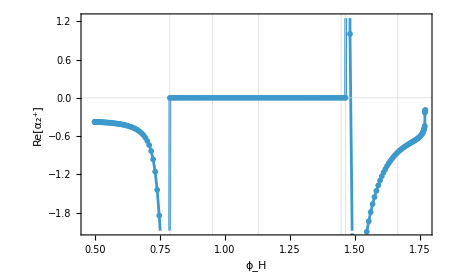
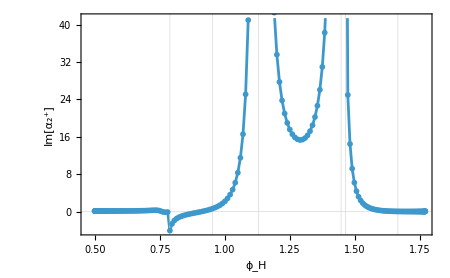

```mathematica
Row[{Show[ListLinePlot[Transpose[{ψHlist,Re[α2Gapped]}],Frame->True,FrameLabel->{"ϕ_H", "Re[α_2^+]"},ImageSize->450,PlotLegends->Automatic,GridLines->{gridlines,{0}},GridLinesStyle->Thick],ListPlot[Transpose[{ψHlist,Re[α2Gapped]}]]],
Show[ListLinePlot[Transpose[{ψHlist,Im[α2Gapped]}],Frame->True,FrameLabel->{"ϕ_H", "Im[α_2^+]"},ImageSize->450,PlotLegends->Automatic,GridLines->{gridlines,{0}},GridLinesStyle->Thick],ListPlot[Transpose[{ψHlist,Im[α2Gapped]}]]]}]
```

Read the sound speed from the QNMs

```mathematica
nn = 1;
cs1Read =Join[Table[Re[(soundModeAll1[[n,;;]]/qlist)[[nn]]],{n,1,idTurning1-1}],Table[ⅈ Im[(soundModeAll1[[n,;;]]/qlist)[[nn]]],{n,idTurning1,idInstability1}],Table[Re[(soundModeAll1[[n,;;]]/qlist)[[nn]]],{n,idInstability1+1,idInstability2-1}],Table[ⅈ Im[(soundModeAll1[[n,;;]]/qlist)[[nn]]],{n,idInstability2,idTurning2}],Table[Re[(soundModeAll1[[n,;;]]/qlist)[[nn]]],{n,idTurning2+1,Nbackgrounds}]];
Clear[nn]
```

```mathematica
cs1ReadSrc = Table[(soundModeAll1[[n, 1 ;; All]]/qlist)[[1]], {n, 1, Nbackgrounds}];
cs2QNM = Re[cs1ReadSrc^2];

ζoversQNM = cs2QNM^2/(Pi (DψHFD . Log[thermo[[All, 1]]/thermo[[All, 3]]])^2);
TΓsQNM = 1/(3 Pi) + ζoversQNM;

tolSrc = 10^-7;
idTurning1Src = First[Flatten[Position[cs2, _?Negative]]];
idTurning2Src = Last[Flatten[Position[cs2, _?Negative]]];
idColl1Src = Position[LightMode1, Select[LightMode1, Abs[Re[#]] <= tolSrc &][[1]]][[1, 1]];
idColl2Src = Position[LightMode1, Select[LightMode1, Abs[Re[#]] <= tolSrc &][[-1]]][[1, 1]];
idInstability1Src = Position[LightMode2, Select[LightMode2, Im[#] > 0 &][[1]]][[1, 1]];
idInstability2Src = Position[LightMode2, Select[LightMode2, Im[#] > 0 &][[-1]]][[1, 1]];
{idColl1Src, idTurning1Src, idInstability1Src, idInstability2Src, idColl2Src, idTurning2Src}
```

{64,83,101,132,135,162}

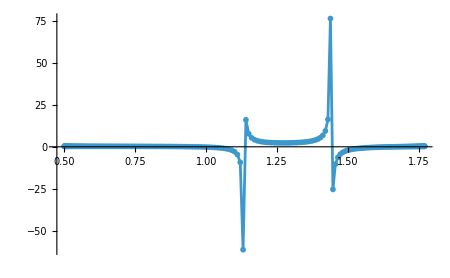
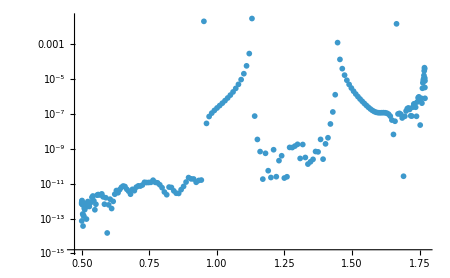

```mathematica
Row[{Show[ListLinePlot[Transpose[{ψHlist,cs2}],PlotRange->All,ImageSize->450],ListPlot[Transpose[{ψHlist,cs1Read^2}]]],Show[ListLogPlot[Transpose[{ψHlist,Abs[cs2-cs1Read^2]}],PlotRange->All,ImageSize->450]]}]
```

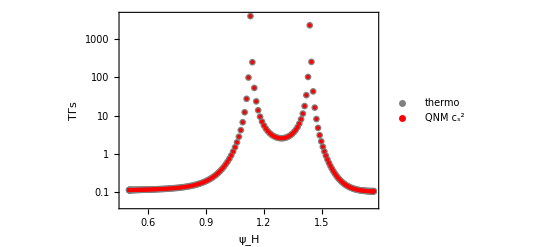
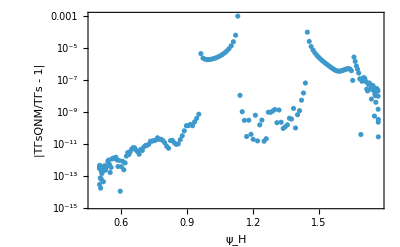

```mathematica
Row[{ListLogPlot[{Transpose[{ψHlist, TΓs}], Transpose[{ψHlist, TΓsQNM}]}, PlotStyle -> {Directive[Gray, PointSize[0.012]], Red}, PlotRange -> All, Frame -> True, FrameLabel -> {"\!\(\*SubscriptBox[\(ψ\), \(H\)]\)", "TΓs"}, PlotLegends -> {"thermo", "QNM \!\(\*SubsuperscriptBox[\(c\), \(s\), \(2\)]\)"}, ImageSize -> 400], ListLogPlot[Transpose[{ψHlist, Abs[TΓsQNM/TΓs - 1]}], Frame -> True, FrameLabel -> {"\!\(\*SubscriptBox[\(ψ\), \(H\)]\)", "|TΓsQNM/TΓs - 1|"}, PlotRange -> All, ImageSize -> 400]}]
```

#### cv/C form 1

```mathematica
Δtilde =√(M2T^2-M1T) ;
A = M1T-2 M2T^2+2M2T Δtilde;
B =ccs2 q2T ;
P =M1T/(q2T (M1T (2M2T-Δtilde)+2 M2T^2(Δtilde-M2T)));

(*When Δ = √(Subscript[M, 1]-Subscript[M, 2]^2) is real*)
ccv1 = 1+M1T/(ccs2 M2T)imα2T;

(*When Δ = √(Subscript[M, 1]-Subscript[M, 2]^2) is imaginary*)
ccv2p = 1/2+imα2T/(B P)+ √(A/B+(1/2+imα2T/(B P))^2);
ccv2m = 1/2+imα2T/(B P)- √(A/B+(1/2+imα2T/(B P))^2);
```

```mathematica
ccvList1=Table[ccv1/.{imα2T-> Im[α2Gapped[[n]]],reα2T-> Re[α2Gapped[[n]]],M1T->EFTparameters[[n,1]],M2T->EFTparameters[[n,2]],ccs2-> cs2[[n]]},{n,1,idColl1Src-1}];

ccvList2p=Table[ccv2p/.{imα2T-> Im[α2Gapped[[n]]],reα2T-> Re[α2Gapped[[n]]],M1T->EFTparameters[[n,1]],M2T->EFTparameters[[n,2]],ccs2-> cs2[[n]],q2T->q02Inter[ψHlist[[n]]]},{n,idColl1Src,idColl2Src}];
ccvList2m=Table[ccv2m/.{imα2T-> Im[α2Gapped[[n]]],reα2T-> Re[α2Gapped[[n]]],M1T->EFTparameters[[n,1]],M2T->EFTparameters[[n,2]],ccs2-> cs2[[n]],q2T->q02Inter[ψHlist[[n]]]},{n,idColl1Src,idColl2Src}];

ccvList3=Table[ccv1/.{imα2T-> Im[α2Gapped[[n]]],reα2T-> Re[α2Gapped[[n]]],M1T->EFTparameters[[n,1]],M2T->EFTparameters[[n,2]],ccs2-> cs2[[n]]},{n,idColl2Src+1,Nbackgrounds}];
```

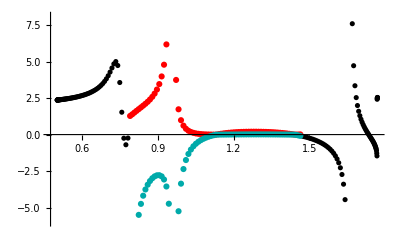

```mathematica
Show[ListPlot[{Transpose[{ψHlist[[1;;idColl1Src-1]],ccvList1}],Transpose[{ψHlist[[idColl2Src+1;;Nbackgrounds]],ccvList3}]},PlotRange->{All,Automatic},PlotStyle->Black],ListPlot[Transpose[{ψHlist[[idColl1Src;;idColl2Src]],ccvList2p}],PlotStyle->Red],ListPlot[Transpose[{ψHlist[[idColl1Src;;idColl2Src]],ccvList2m}],PlotStyle->Darker@Cyan],ImageSize->400]
```

```mathematica
ccvList = Join[ccvList1, ccvList2p[[1 ;; idTurning1Src - idColl1Src]], ccvList2m[[idTurning1Src - idColl1Src + 1 ;; idInstability1Src - idColl1Src]], ccvList2p[[idInstability1Src - idColl1Src + 1 ;; idInstability2Src + 1 - idColl1Src]], ccvList2m[[idInstability2Src + 2 - idColl1Src ;; -1]], ccvList3];
Dimensions[ccvList]
Nbackgrounds
```

{200}

200

#### cv/C form 2

```mathematica
z1=-imα2 imΩp+2 reα2 reΩp+(imα2 reΩp^2)/imΩp/.{imα2-> imα2T/(2 π T),reα2-> reα2T/(2 π T),imΩp-> 2 π T imΩpT,reΩp-> 2 π T reΩpT,imΩm-> 2 π T imΩmT,reΩm-> 2 π T reΩmT}//Simplify[#,{T>0}]&

ccv1=1-(imα2 (imΩp^2+reΩp^2))/(ccs2 imΩp)/.{imα2-> imα2T/(2 π T),reα2-> reα2T/(2 π T),imΩp-> 2 π T imΩpT,reΩp-> 2 π T reΩpT,imΩm-> 2 π T imΩmT,reΩm-> 2 π T reΩmT}//Simplify[#,{T>0}]&
```

-imα2T imΩpT+2 reα2T reΩpT+(imα2T reΩpT^2)/imΩpT

1-(imα2T (imΩpT^2+reΩpT^2))/(ccs2 imΩpT)

```mathematica
z2 = imα2 (imΩm-imΩp)+((-1+cvsol) ccs2 imΩm)/imΩp/.{imα2-> imα2T/(2 π T),reα2-> reα2T/(2 π T),imΩp-> 2 π T imΩpT,reΩp-> 2 π T reΩpT,imΩm-> 2 π T imΩmT,reΩm-> 2 π T reΩmT}//Simplify[#,{T>0}]&
ccv21 = 1/(2 ccs2 imΩm q02)(ccs2 imΩm q02+imα2 imΩp (-imΩm+imΩp) q02-√(q02 (-4 ccs2 imΩm^2 imΩp^2+(ccs2 imΩm+imα2 imΩp (-imΩm+imΩp))^2 q02)))/.{imα2-> imα2T/(2 π T),reα2-> reα2T/(2 π T),imΩp-> 2 π T imΩpT,reΩp-> 2 π T reΩpT,imΩm-> 2 π T imΩmT,reΩm-> 2 π T reΩmT,q02-> q2T (2 π T)^2}/.T->1//Simplify//FullSimplify[#,{T>0}]&
ccv22 = 1/(2 ccs2 imΩm q02)(ccs2 imΩm q02+imα2 imΩp (-imΩm+imΩp) q02+√(q02 (-4 ccs2 imΩm^2 imΩp^2+(ccs2 imΩm+imα2 imΩp (-imΩm+imΩp))^2 q02)))/.{imα2-> imα2T/(2 π T),reα2-> reα2T/(2 π T),imΩp-> 2 π T imΩpT,reΩp-> 2 π T reΩpT,imΩm-> 2 π T imΩmT,reΩm-> 2 π T reΩmT,q02-> q2T (2 π T)^2}/.T->1//Simplify//FullSimplify[#,{T>0}]&
```

imα2T (imΩmT-imΩpT)+(ccs2 (-1+cvsol) imΩmT)/imΩpT

(ccs2 imΩmT q2T+imα2T imΩpT (-imΩmT+imΩpT) q2T-√(q2T (-4 ccs2 imΩmT^2 imΩpT^2+(ccs2 imΩmT+imα2T imΩpT (-imΩmT+imΩpT))^2 q2T)))/(2 ccs2 imΩmT q2T)

(ccs2 imΩmT q2T+imα2T imΩpT (-imΩmT+imΩpT) q2T+√(q2T (-4 ccs2 imΩmT^2 imΩpT^2+(ccs2 imΩmT+imα2T imΩpT (-imΩmT+imΩpT))^2 q2T)))/(2 ccs2 imΩmT q2T)

Gapped modes with finite real part (n < idColl1 and n > idColl2): single root ccv1, z1.

```mathematica
nFinite = Join[Range[1, idColl1 - 1], Range[idColl2 + 1, Nbackgrounds]];

ccvList1 = Table[ccv1 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]]}, {n, nFinite}];

zList1 = Table[z1 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]]}, {n, nFinite}];

Flatten[{Dimensions[zList1], Dimensions[ccvList1]}]
```

{128,128}

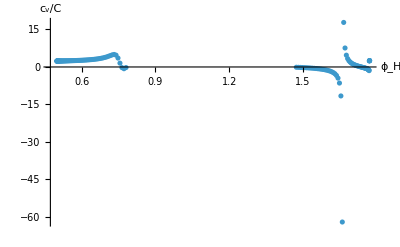

```mathematica
ListPlot[Transpose[{ψHlist[[nFinite]], ccvList1}], AxesLabel -> {"\!\(\*SubscriptBox[\(ϕ\), \(H\)]\)", "\!\(\*SubscriptBox[\(c\), \(v\)]\)/C"}, PlotRange -> All, ImageSize -> 400]
```

Gapped modes with vanishing real part (idColl1 <= n <= idColl2): two roots, ccv21 and ccv22.

```mathematica
ccvList21 = Table[ccv21 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]], q2T -> q02Inter[ψHlist[[n]]]}, {n, idColl1, idColl2}];

zList21 = Table[z2 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]], q2T -> q02Inter[ψHlist[[n]]]} /. cvsol -> ccvList21[[n - idColl1 + 1]], {n, idColl1, idColl2}];

ccvList22 = Table[ccv22 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]], q2T -> q02Inter[ψHlist[[n]]]}, {n, idColl1, idColl2}];

zList22 = Table[z2 /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]], q2T -> q02Inter[ψHlist[[n]]]} /. cvsol -> ccvList22[[n - idColl1 + 1]], {n, idColl1, idColl2}];

Flatten[{Dimensions[zList21], Dimensions[ccvList21]}]

Flatten[{Dimensions[zList22], Dimensions[ccvList22]}]

Dimensions[ψHlist[[idColl1 ;; idColl2]]]
```

{72,72}

{72,72}

{72}

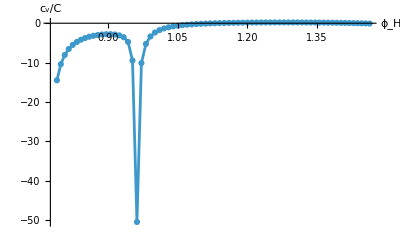
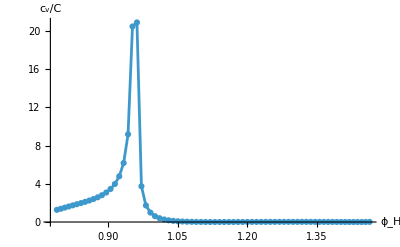

```mathematica
Row[{Show[ListLinePlot[Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList21}], AxesLabel -> {"\!\(\*SubscriptBox[\(ϕ\), \(H\)]\)", "\!\(\*SubscriptBox[\(c\), \(v\)]\)/C"}, PlotRange -> All, ImageSize -> 400], ListPlot[Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList21}]]], Show[ListLinePlot[Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList22}], AxesLabel -> {"\!\(\*SubscriptBox[\(ϕ\), \(H\)]\)", "\!\(\*SubscriptBox[\(c\), \(v\)]\)/C"}, PlotRange -> All, ImageSize -> 400], ListPlot[Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList22}]]]}]
```

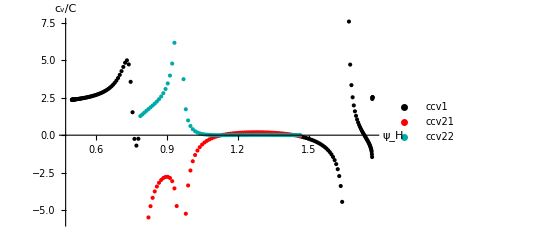

```mathematica
ListPlot[{Transpose[{ψHlist[[nFinite]], ccvList1}], Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList21}], Transpose[{ψHlist[[idColl1 ;; idColl2]], ccvList22}]}, PlotStyle -> {Black, Red, Darker[Cyan]}, ImageSize -> 400, AxesLabel -> {"\!\(\*SubscriptBox[\(ψ\), \(H\)]\)", "\!\(\*SubscriptBox[\(c\), \(v\)]\)/C"}, PlotLegends -> {"ccv1", "ccv21", "ccv22"}]
```

```mathematica
ccvListTΓ = Table[Which[n < idColl1Src || n > idColl2Src, ccv1, n < idTurning1Src, ccv22, n < idInstability1Src, ccv21, n <= idInstability2Src, ccv21, True, ccv21] /. {imα2T -> Im[α2Gapped[[n]]], reα2T -> Re[α2Gapped[[n]]], imΩpT -> Im[TrackLightModeC[[n]]], reΩpT -> Re[TrackLightModeC[[n]]], imΩmT -> Im[TrackLightMode[[n]]], reΩmT -> Re[TrackLightMode[[n]]], ccs2 -> cs2[[n]], q2T :> q02Inter[ψHlist[[n]]]}, {n, 1, Nbackgrounds}];
Max[Abs[ccvListTΓ - ccvList]]
```

0.

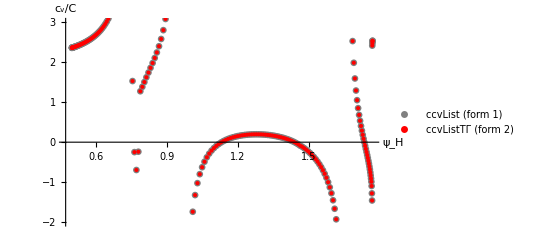

```mathematica
ListPlot[{Transpose[{ψHlist, ccvList}], Transpose[{ψHlist, ccvListTΓ}]}, PlotStyle -> {Directive[Gray, PointSize[0.012]], Red}, PlotRange -> {All, {-2, 3}}, ImageSize -> 400, AxesLabel -> {"\!\(\*SubscriptBox[\(ψ\), \(H\)]\)", "\!\(\*SubscriptBox[\(c\), \(v\)]\)/C"}, PlotLegends -> {"ccvList (form 1)", "ccvListTΓ (form 2)"}]
```

#### Z_s/Z_0

```mathematica
z= -M1/q02 ccv^-1/.{q02-> q2T (2 π T)^2,M1-> M1T (2 π T)^2 }//FullSimplify;
```

```mathematica
zList=Table[z/.{M1T-> EFTparameters[[n,1]],ccv->ccvList[[n]],q2T-> q02Inter[ψHlist[[n]]]},{n,1,Nbackgrounds}];
Dimensions[zList]
```

InterpolatingFunction::dmval: Input value {1.7604493919359701490699991644827031258273261376904073095852695608468277201816691998323125389309337} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.76210349062510756418878037077376213709148361635345439873846296433530526144623876175678606725451275} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.76360130197735379172829805924524377693939259061212212666282805509440218307771546776613086057001198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{200}

```mathematica
zListTΓ = Table[z /. {M1T -> EFTparameters[[n, 1]], ccv -> ccvListTΓ[[n]], q2T -> q02Inter[ψHlist[[n]]]}, {n, 1, Nbackgrounds}];
Dimensions[zListTΓ]
```

InterpolatingFunction::dmval: Input value {1.7604493919359701490699991644827031258273261376904073095852695608468277201816691998323125389309337} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.76210349062510756418878037077376213709148361635345439873846296433530526144623876175678606725451275} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.76360130197735379172829805924524377693939259061212212666282805509440218307771546776613086057001198} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{200}

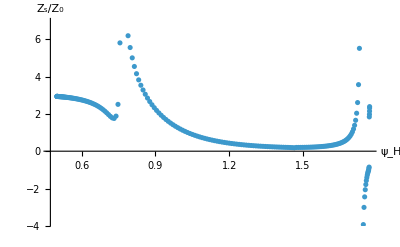

```mathematica
ListPlot[Transpose[{ψHlist,zList}],ImageSize->400,AxesLabel->{"ψ_H","Z_s/Z_0"}]
```

```mathematica
Clear[z,ccv1,ccv2m,ccv2p,A,B,P,Δtilde,ccvList1,ccvList2m,ccvList2p,ccvList3]
```

### Γ

If higher number of grid points Nu speed of sound is loaded, results improve without having to increase Nu for the QNM computation

```mathematica
thermoNz80 = Import["./background_data/phiM=0.8_phiQ=10._a=0._N_80_200_backgrounds.m"][[2]];
cs2Nz80 = (DψHFD . Log[thermoNz80[[All, 1]]/thermoNz80[[All, 3]]])/(DψHFD . Log[thermoNz80[[All, 2]]/thermoNz80[[All, 3]]^3]);
{Dimensions[cs2Nz80], Max[Abs[cs2Nz80/cs2 - 1]]}
```

{{200},0.00002442901536001180953556841238747050092878832992877171740506120471497712230623763892164125}

Plots of sound ω vs q

```mathematica
nback =idTurning1+2;
If[idTurning1<=nback<=idInstability1||idInstability2<=nback<=idTurning2,{normRe,normIm} ={3,1},{normRe,normIm} ={1,2}];
```

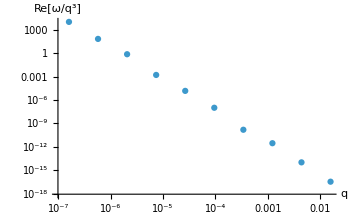
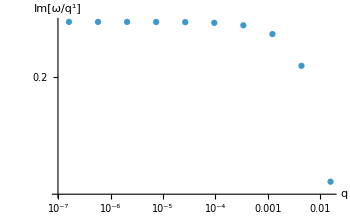

```mathematica
Row[{ListLogLogPlot[{Transpose[{qlist,Abs[Re[soundModeAll1[[nback]]]/qlist^normRe]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Re[ω/q^(`1`)]"][normRe]}],ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback]]]/qlist^normIm]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Im[ω/q^(`1`)]"][normIm]}]}]
```

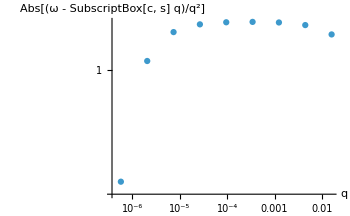
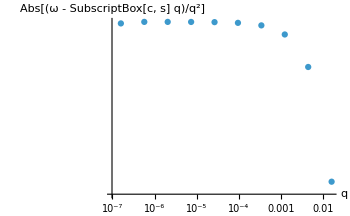

```mathematica
Row[{ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback,;;]]-cs1Read[[nback]]qlist]/qlist^2]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Abs[(ω - SubscriptBox[c, s] q)/q^2]"][normRe]}],ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback,;;]]-√cs2[[nback]] qlist]/qlist^2]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Abs[(ω - SubscriptBox[c, s] q)/q^2]"][normRe]}](*,ListLogLogPlot[{Transpose[{qlist,Abs[Im[soundModeAll1[[nback,;;]]-√cs2ThermoNz80[[nback]] qlist]/qlist^2]}]},ImageSize->350,AxesLabel->{"q",StringTemplate["Abs[(ω - SubscriptBox[c, s]q)/q^2]"][normRe]}]*)}]
```

Extract α_(2,s) from different values of small momenta

```mathematica
α2SoundImTable = 
    Table[(Im[soundModeAll1[[n, ;;]] - cs1Read[[n]] qlist]/(qlist^2))[[
         m]], {m, 1, Nq}, {n, 1, Nbackgrounds}];
α2SoundImTableThermo = 
    Table[(Im[soundModeAll1[[n, ;;]] - Sqrt[cs2[[n]]] qlist]/(
           qlist^2))[[m]], {m, 1, Nq}, {n, 1, Nbackgrounds}];
α2SoundImTableThermoNz80 = 
  Table[(Im[
       soundModeAll1[[n, ;;]] - Sqrt[cs2Nz80[[n]]] qlist]/(qlist^2))[[
    m]], {m, 1, Nq}, {n, 1, Nbackgrounds}];
legends = 
    Table["q/T = " <> 
        ToString[
          NumberForm[N[2 π qlist[[n]]], 2, 
            ExponentFunction -> (Null &)]], {n, 1, 
        Length[α2SoundImTable]}];
{Dimensions[α2SoundImTable], 
  Dimensions[α2SoundImTableThermo], Dimensions[α2SoundImTableThermoNz80]}
```

{{10,200},{10,200},{10,200}}

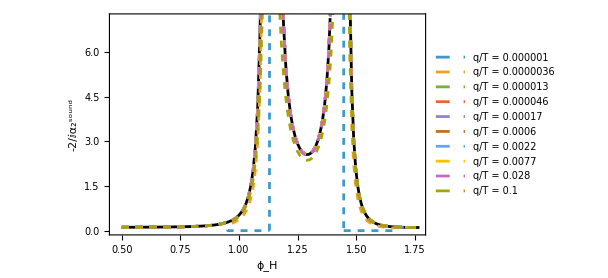
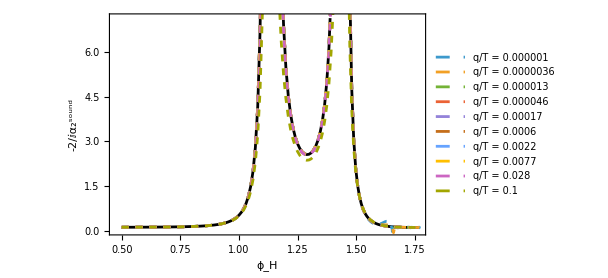

```mathematica
Row[{Show[ListLinePlot[Transpose[{ψHlist,TΓs}],PlotStyle->Black,Frame->True,FrameLabel->{"ϕ_H", "-2/ⅈα_2^sound"},ImageSize->450],ListLinePlot[Table[Transpose[{ψHlist,-2 α2SoundImTable[[m]]/(2 π)}],{m,1,Length[α2SoundImTable]}],PlotLegends->legends,PlotStyle->Dashed,PlotRange->All]],Show[ListLinePlot[Transpose[{ψHlist,TΓs}],PlotStyle->Black,Frame->True,FrameLabel->{"ϕ_H", "-2/ⅈα_2^sound"},ImageSize->450],ListLinePlot[Table[Transpose[{ψHlist,-2 α2SoundImTableThermo[[m]]/(2 π)}],{m,1,Length[α2SoundImTableThermo]}],PlotLegends->legends,PlotStyle->Dashed,PlotRange->All]]}]
```

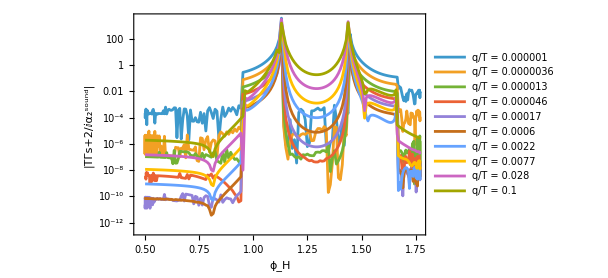
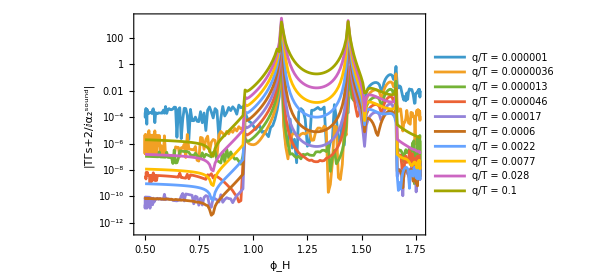

```mathematica
Row[{Show[ListLogPlot[Table[Transpose[{ψHlist,Abs[-2 α2SoundImTable[[m]]/(2 π)-TΓs]}],{m,1,Length[α2SoundImTable]}],Frame->True,FrameLabel->{"ϕ_H", "|TΓs+2/ⅈα_2^sound|"},ImageSize->450,PlotLegends->legends,Joined->True]],Show[ListLogPlot[Table[Transpose[{ψHlist,Abs[-2 α2SoundImTableThermo[[m]]/(2 π)-TΓs]}],{m,1,Length[α2SoundImTableThermo]}],Frame->True,FrameLabel->{"ϕ_H", "|TΓs+2/ⅈα_2^sound|"},ImageSize->450,PlotLegends->legends,Joined->True]]}]
```

```mathematica
TΓα2 =-T(2 ccs2 (-1+ccv) M2)/M1+TTΓΓs/.{M1-> M1T (2 π T)^2,M2-> M2T 2 π T}//Simplify
```

-(ccs2 (-1+ccv) M2T)/(M1T π)+TTΓΓs

```mathematica
TΓα2ListThermo = Table[TΓα2 /. {M1T -> EFTparameters[[n, 1]],  M2T -> EFTparameters[[n, 2]], ccs2 -> cs2[[n]], ccv -> ccvListTΓ[[n]],TTΓΓs -> TΓs[[n]]},{n, 1, Nbackgrounds}];
TΓα2ListTable = 
Table[TΓα2 /. {M1T -> EFTparameters[[n, 1]],  M2T -> EFTparameters[[n, 2]], ccs2 -> cs2[[n]],  ccv -> ccvListTΓ[[n]], TTΓΓs -> -2 α2SoundImTable[[m,n]]/(2 Pi)}, {m, 1, 
    Length[α2SoundImTable]}, {n, 1, 
        Nbackgrounds}];
TΓα2ListTablecs2Thermo = Table[TΓα2 /. {M1T -> EFTparameters[[n, 1]], M2T -> EFTparameters[[n, 2]], ccs2 -> cs2[[n]], ccv -> ccvListTΓ[[n]], TTΓΓs ->  -2 α2SoundImTableThermo[[m, n]]/(2 Pi)}, {m, 1, Length[α2SoundImTableThermo]}, {n, 1, Nbackgrounds}];
TΓα2ListTablecs2ThermoNz80 = Table[TΓα2 /. {M1T -> EFTparameters[[n, 1]], M2T -> EFTparameters[[n, 2]], ccs2 -> cs2Nz80[[n]], ccv -> ccvListTΓ[[n]], TTΓΓs -> -2 α2SoundImTableThermoNz80[[m, n]]/(2 Pi)}, {m, 1, Length[α2SoundImTableThermoNz80]}, {n, 1, Nbackgrounds}];
{Dimensions[TΓα2ListTable], Dimensions[TΓα2ListTablecs2Thermo], Dimensions[TΓα2ListTablecs2ThermoNz80]}
```

{{10,200},{10,200},{10,200}}

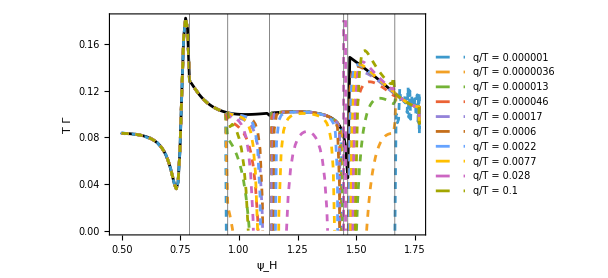

```mathematica
Show[ListLinePlot[Transpose[{ψHlist,TΓα2ListThermo}],PlotStyle->Black,ImageSize->450,Frame->True,GridLines->{gridlines,None},GridLinesStyle->Darker[Gray],FrameLabel->{"ψ_H","T Γ"}],ListLinePlot[Table[Transpose[{ψHlist,TΓα2ListTable[[m]]}],{m,1,Length[TΓα2ListTable]}],PlotLegends->legends,PlotStyle->Dashed]]
```

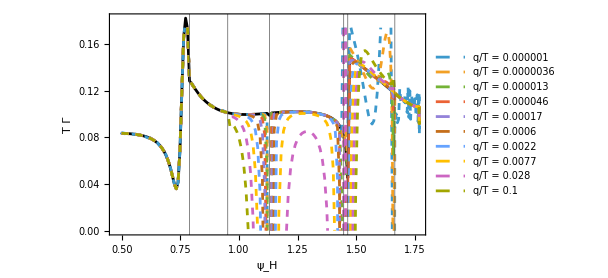

```mathematica
Show[ListLinePlot[Transpose[{ψHlist,TΓα2ListThermo}],PlotStyle->Black,ImageSize->450,Frame->True,GridLines->{gridlines,None},GridLinesStyle->Darker[Gray],FrameLabel->{"ψ_H","T Γ"}],ListLinePlot[Table[Transpose[{ψHlist,TΓα2ListTablecs2Thermo[[m]]}],{m,1,Length[TΓα2ListTablecs2Thermo]}],PlotLegends->legends,PlotStyle->Dashed]]
```

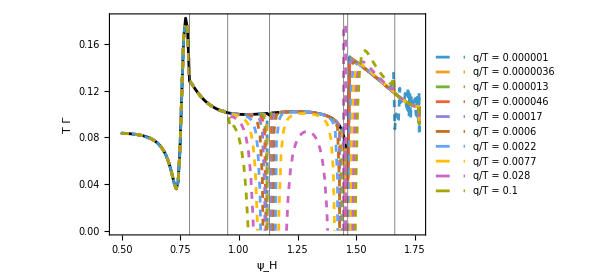

```mathematica
Show[ListLinePlot[
    Transpose[{ψHlist, TΓα2ListThermo}], 
    PlotStyle -> Black, ImageSize -> 450, Frame -> True, 
    GridLines -> {gridlines, None}, GridLinesStyle -> Darker[Gray], 
    FrameLabel -> {"\!\(\*SubscriptBox[\(ψ\), \(H\)]\)", 
        "T Γ"}], 
  ListLinePlot[
    Table[Transpose[{ψHlist, 
          TΓα2ListTablecs2ThermoNz80[[m]]}], {m, 1, 
        Length[TΓα2ListTablecs2ThermoNz80]}], 
    PlotLegends -> legends, PlotStyle -> Dashed]]
```

### Save EFT parameters

```mathematica
EFTparametersFile = "./EFT-parameters-phiM=" <> ToString[N[ϕM /. constants]] <> "_Nz_" <> ToString[Nu] <> ".m";
Export[EFTparametersFile, {cs2, q02Inter[ψHlist], EFTparameters[[All, 1]], EFTparameters[[All, 2]], ccvListTΓ, zListTΓ, TΓα2ListThermo}]
```

## 5. QNMs vs EFT

#### Load Background

```mathematica
{fields, thermo, constants, ℰH, ℰL, Tc, ψHlist} = Import["./background_data/phiM=0.8_phiQ=10._a=0._N_40_200_backgrounds.m"];
VV[ϕ_] := -3 - (3 ϕ^2)/2 - ϕ^4/3 - (4 𝒶^2 ϕ^16)/3 + 2/3 ϕ^12 (𝒶 (1/ϕM^2 + 72/ϕQ) - 2/ϕQ^2) + ϕ^6 (1/(2 ϕM^4) - 1/(3 ϕM^2) - 2/ϕQ) + (8 𝒶 ϕ^14 (-1 + 12 𝒶 ϕQ))/(3 ϕQ) + ϕ^8 (-4 𝒶 - (72 ϕM^2 - 16 ϕM^4 + ϕQ)/(12 ϕM^4 ϕQ)) + ϕ^10 (𝒶 (4/3 - 8/ϕM^2) + (2 (27 + ϕQ/ϕM^2))/(3 ϕQ^2)) /. constants
𝓌Hydro[q_, cs2_, TΓ_] := (Sqrt[cs2] q - I π TΓ q^2)
DψH = Cheb[ψHlist[[1]], ψHlist[[-1]], Length[ψHlist], 100][[2]];
DψHFD = NDSolve`FiniteDifferenceDerivative[1, ψHlist, "DifferenceOrder" -> 8]["DifferentiationMatrix"];
cs2Thermo = DψHFD . (thermo[[;; , 6]]/thermo[[;; , 3]]^4)/DψHFD . (thermo[[;; , 5]]/thermo[[;; , 3]]^4);
ζovers = 1/π (DψHFD . (Log[thermo[[;; , 2]]/thermo[[;; , 3]]^3]))^-2;
TΓThermo = (1/(3 π) + ζovers);
idCrit = Position[cs2Thermo, Min[cs2Thermo]][[1, 1]];
Nbackgrounds = Length[ψHlist];
Print["\!\(\*SubscriptBox[\(N\), \(backgrounds\)]\) = " <> ToString[Nbackgrounds]]
constants
```

N_backgrounds = 200

{κ→1,ϕM→4/5,ϕQ→10,𝒶→0}

```mathematica
prec = MachinePrecision(*30*);
Nu=Dimensions[fields][[3]]
u=SetPrecision[Reverse[Table[1/2+1/2 Cos[((j-1) π)/(Nu-1)],{j,1,Nu}]],prec];
Du = NDSolve`FiniteDifferenceDerivative[1, u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
Du2 = NDSolve`FiniteDifferenceDerivative[2,u, "DifferenceOrder" -> "Pseudospectral"]["DifferentiationMatrix"];
grid = {u,Du,Du2};
u = grid[[1]];
u//Precision
```

40

MachinePrecision

#### Load EFT parameters and EFT dispersion relation

```mathematica
{cs2, q02T, M1T, M2T, ccv, z, ΓT} = Import["./EFT-parameters-phiM=" <> ToString[N[ϕM /. constants]] <> "_Nz_" <> ToString[Nu] <> ".m"];
Dimensions[{cs2, q02T, M1T, M2T, ccv, z, ΓT}]
```

{7,200}

```mathematica
dispEFT = -I (2 π ΓT 𝓆^2 - I 𝓌) 𝓌 (M1T + z 𝓆^2 + (-2 I M2T - 𝓌) 𝓌) + cs2 𝓆^2 (M1T + ccv z 𝓆^2 + ccv (-2 I M2T - 𝓌) 𝓌);
```

```mathematica
Dimensions[dispEFT]
```

{200}

```mathematica
{LightMode1, LightMode2} = Import["./datawgapped_phiM=" <> ToString[N[ϕM /. constants]] <> "_phiQ=" <> ToString[N[ϕQ /. constants]] <> "_Nz_" <> ToString[Nu] <> "_.m"];
tolSwitch = 10^-7;
{idColl1, idColl2} = Flatten[Position[LightMode1, x_ /; Abs[Re[x]] <= tolSwitch, {1}]][[{1, -1}]];
{idInstability1, idInstability2} = Flatten[Position[LightMode2, x_ /; Im[x] > 0, {1}]][[{1, -1}]];
{idTurning1, idTurning2} = Flatten[Position[cs2, x_ /; x < 0, {1}]][[{1, -1}]];
{idColl1, idTurning1, idInstability1, idInstability2, idColl2, idTurning2}
```

{64,83,101,132,135,162}

### Tracking sound and first gapped at fixed T - using EFT modes as guess at low q

```mathematica
BackgroundIndeces = {49, 82, 92, 116, 160, 170};
```

```mathematica
ψHlist[[BackgroundIndeces[[5]]]]
```

```mathematica
backgroundNumber=6;
number =BackgroundIndeces[[backgroundNumber]];
T = thermo[[number,1]]
e = thermo[[number,5]];
Λ = thermo[[number,3]];
cs2[[number]]
ccv[[number]]
```

```mathematica
{qmin,qmax} = {5/100,10};
Nq=100;
qlist = 1/(2 π)Range[qmin,qmax,(qmax-qmin)/(Nq-1)];
```

```mathematica
qmin//N
```

#### EFT modes

```mathematica
EFTModes = Table[𝓌 /. NSolve[dispEFT[[number]] /. 𝓆 -> qlist[[n]], 𝓌], {n, 1, Nq}];
Dimensions[EFTModes]
```

```mathematica
InterIndex = 17(*80*);
Row[{Show[
   ListPlot[
    Table[Transpose[{2 π qlist, 
       Re[EFTModes[[;; , n]]]}], {n, 1, 4}], Frame -> True, 
    FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
      "Re[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
    ImageSize -> 450], 
   ListPlot[
    Table[{2 π qlist[[InterIndex]], 
      Re[EFTModes[[InterIndex, m]]]}, {m, 1, 4}], 
    PlotStyle -> Black]], 
  Show[ListPlot[
    Table[Transpose[{2 π qlist, 
       Im[EFTModes[[;; , n]]]}], {n, 1, 4}], Frame -> True, 
    FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
      "Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
    ImageSize -> 450], 
   ListPlot[
    Table[{2 π qlist[[InterIndex]], 
      Im[EFTModes[[InterIndex, m]]]}, {m, 1, 4}], 
    PlotStyle -> Black]]}]
```

```mathematica
distinctNearest[list_, targets_] := Module[{avail = list, out = {}, id}, Do[id = First[Ordering[Abs[avail - t], 1]]; AppendTo[out, avail[[id]]]; avail = Delete[avail, id], {t, targets}]; out];

OrderedModesR = {};
aux = EFTModes[[-1]];
Do[
  aux = distinctNearest[EFTModes[[Nq - n, ;;]], aux];
  AppendTo[OrderedModesR, aux];
  , {n, 0, Nq - 1}];
OrderedModesR = Reverse[OrderedModesR];

OrderedModesL = {};
aux = EFTModes[[1]];
Do[
  aux = distinctNearest[EFTModes[[n, ;;]], aux];
  AppendTo[OrderedModesL, aux];
  , {n, 1, Nq}];

OrderedModesInter = {};
aux = EFTModes[[InterIndex]];
Do[
  aux = distinctNearest[EFTModes[[n, ;;]], aux];
  AppendTo[OrderedModesInter, aux];
  , {n, InterIndex, 1, -1}];
OrderedModesInter = Reverse[OrderedModesInter];
aux = OrderedModesInter[[-1]];
Do[
  aux = distinctNearest[EFTModes[[n, ;;]], aux];
  AppendTo[OrderedModesInter, aux];
  , {n, InterIndex + 1, Nq}];

{Dimensions[OrderedModesL], Dimensions[OrderedModesR], Dimensions[OrderedModesInter]}
```

```mathematica
Dimensions[OrderedModesInter[[;; , 1]]]
Dimensions[qlist[[1 ;; InterIndex]]]
```

```mathematica
Row[{Show[
      ListPlot[
        Table[
     Transpose[{2 π qlist, Re[OrderedModesR[[;; , n]]]}], {n,
             1, 4}], Frame -> True, 
        FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
            "Re[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
        ImageSize -> 450, PlotRange -> All], 
      ListPlot[
        Table[
     Transpose[{2 π qlist, Re[OrderedModesL[[;; , n]]]}], {n,
             1, 4}]], 
      Plot[{Re[𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
              TΓThermo[[number]]]], 
          Re[𝓌Hydro[-k/(2 π), cs2Thermo[[number]], 
              TΓThermo[[number]]]]}, {k, 0, 
     2 π qmax}]]}]
```

```mathematica
Row[{Show[
      ListPlot[
        Table[
     Transpose[{2 π qlist, Im[OrderedModesL[[;; , n]]]}], {n,
             1, 4}], Frame -> True, 
        FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
            "Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
        ImageSize -> 450, PlotRange -> All], 
      Plot[{Im[𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
              TΓThermo[[number]]]], 
          Im[𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
              TΓThermo[[number]]]]}, {k, 0, qmax}]]}]
```

```mathematica
Show[ListPlot[
  Table[Transpose[{2 π qlist, 
     Re[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
  Frame -> True, 
  FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
    "Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
  ImageSize -> 450, PlotRange -> All]]
Show[ListPlot[
  Table[Transpose[{2 π qlist, 
     Im[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
  Frame -> True,
  FrameLabel -> {"\!\(\*FractionBox[\(q\), \(T\)]\)", 
    "Im[\!\(\*FractionBox[\(ω\), \(2  πT\)]\)]"}, 
  ImageSize -> 450, PlotRange -> All]]
```

```mathematica
it = 1;
2 π qlist[[it]]
EFTModes[[it]] 
𝓌Hydro[qlist[[it]], cs2Thermo[[it]], 
  TΓThermo[[it]]]
Clear[it]
```

```mathematica
Precision[EFTModes]
```

#### QNMs

```mathematica
NQNMs = 0; eigenfunctions = False;
gap = 10^-3;
qcutoff = 1/(2 π)(*2.5*) 1;
QNMs = {};
gappedModes = {};
solnumber = 0;
ImωgappedCutoff = 5;
tol = 10^-1;
Monitor[Do[solnumber += 1;
     q = qlist[[n]];
     (*Track the conjugate pairs*)
     QNM1 = 
      GetQNM[grid, fields[[number]], VV, q, T, prec, NQNMs, 
       eigenfunctions];
     
     If[Abs[q] < qcutoff,
      modes = EFTModes[[n]];
      ,
      modes = QNMs[[-1]];
      ];
     
     aux = {}; avail = QNM1;
Do[
  id = First[Ordering[Abs[avail - modes[[i]]], 1]];
  AppendTo[aux, avail[[id]]];
  avail = Delete[avail, id];
  , {i, 1, Length[modes]}];
     
     AppendTo[QNMs, aux];
     AppendTo[gappedModes, 
      Select[QNM1, 
       Abs[Im[#]] <= ImωgappedCutoff && # != ∞ && # !=
           0 && Abs[Im[#]] >= tol &]];
     
     , {n, 1, Nq}];, {solnumber, QNMs[[-1]], 
    gappedModes[[-1]]}]; // AbsoluteTiming
Clear[aux, id, q, QNM1]
{Precision[QNMs], Precision[gappedModes]}
```

```mathematica
Row[{Show[ListPlot[Table[Transpose[{2 π qlist,Re[QNMs[[;;,n]]]}],{n,1,4}],Frame->True,FrameLabel->{"q/T","Re[ω/(2  πT)]"},ImageSize->450,PlotRange->All],Plot[{Re[𝓌Hydro[k/(2 π),cs2Thermo[[number]],TΓThermo[[number]]]],Re[𝓌Hydro[-k/(2 π),cs2Thermo[[number]],TΓThermo[[number]]]]},{k,0,2 π qmax}]],Show[ListPlot[Table[Transpose[{2 π qlist,Im[QNMs[[;;,n]]]}],{n,1,4}],Frame->True,FrameLabel->{"q/T","Im[ω/(2  πT)]"},ImageSize->450,PlotRange->All],Plot[{Im[𝓌Hydro[k/(2 π),cs2Thermo[[number]],TΓThermo[[number]]]],Im[𝓌Hydro[k/(2 π),cs2Thermo[[number]],TΓThermo[[number]]]]},{k,0,qmax}]]}]
```

```mathematica
QNMs[[-1]]
```

#### Comparison between QNMs and EFT

```mathematica
Quiet[CreateDirectory["./QNM vs EFT data/phiM=0.8", 
   CreateIntermediateDirectories -> True]];
Export["./QNM vs EFT data/phiM=0.8/Modes-background-" <> 
  ToString[backgroundNumber] <> ".m", {qlist, gappedModes, 
  OrderedModesL, OrderedModesR, 
  OrderedModesInter, QNMs}]
```

```mathematica
gappedModesSelected = Table[Select[gappedModes[[n]],Abs[Im[#]]<=3&],{n,1,Nq}];
```

```mathematica
SortBy[gappedModesSelected[[1]],-Im[#]&]
```

```mathematica
backgroundNumber
```

```mathematica
tickLabels[{a_, b_, s_}] := 
    Table[{x, 
        MaTeX[ToString@NumberForm[x, {3, 1}], 
     Magnification -> 1.4]}, {x, 
        a, b, s}];

{xticks, yticks} = 
    Switch[backgroundNumber, 
      1, {tickLabels[{0, 7, 1}], tickLabels[{0, 15, 5}]}, 
      2, {tickLabels[{0, 4, 1}], tickLabels[{0, 1, 0.2}]}, 
      3, {tickLabels[{0, 6, 1}], tickLabels[{0, 6, 1}]}, 
      4, {tickLabels[{0, 10, 2}], tickLabels[{0, 10, 2}]}, 
      5, {tickLabels[{0, 4, 1}], tickLabels[{0, 5, 1}]}, 
      6, {tickLabels[{0, 4, 1}], tickLabels[{0, 6, 1}]}, 
      7, {tickLabels[{0, 10, 2}], tickLabels[{0, 10, 2}]}];

range = Switch[backgroundNumber, 1, {{0, 7}, {0, 15}}, 
      2, {{0, 4}, {0, 1}}, 
   3, {{0, 6}, {0, 6}}, 4, {{0, 10}, {0, 10}}, 
      5, {{0, 4}, {0, 5}}, 6, {{0, 4}, {0, 6}}, 7, {{0, 10}, {0, 10}}];
```

```mathematica
plot1 = Show[
  ListPlot[
   Table[Table[{2 π qlist[[n]], 
      2 π Re[gappedModesSelected[[n, m]]]}, {m, 1, 
      Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}], 
   PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, 
   PlotRange -> range, BaseStyle -> texStyle, 
   FrameLabel -> MaTeX[{"q/T", "\\Re\\omega/T"}, Magnification -> 1.4](*,
   FrameTicks->{{yticks,None},{xticks,None}}*)], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, 
      2 π Re[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Darker@Red, PlotRange -> All], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, -2 π Re[
        OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Red, PlotRange -> All], 
  Plot[{Re[
     2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]], 
    Re[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, 
   PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}], 
  ListPlot[
   Table[Transpose[{2 π qlist, 2 π Re[QNMs[[;; , n]]]}], {n, 
     1, 4}], PlotStyle -> Black]]
```

```mathematica
backgroundNumber
```

```mathematica
tickLabelsClean[{a_,b_,s_}]:=Table[{x,MaTeX[ToString@NumberForm[If[Abs[x]>=10^-15,x,0.0],{3,1}],Magnification->1.4]},{x,a,b,s}];

{xticks,yticks}=Switch[backgroundNumber,1,{tickLabels[{0,7,1}],tickLabels[{-12,0,2}]},2,{tickLabels[{0,4,1}],tickLabels[{-2.5,0,0.5}]},3,{tickLabels[{0,6,1}],tickLabels[{-3.0,0.5,0.5}]},4,{tickLabels[{0,10,2}],tickLabels[{-3.0,1.,1.}]},5,{tickLabels[{0,4,1}],tickLabelsClean[{-3.0,1.0,0.2}]},6,{tickLabels[{0,4,1}],tickLabels[{-0.8,0,0.2}]},7,{tickLabels[{0,10,2}],tickLabels[{-18,2,2}]}];

range=Switch[backgroundNumber,1,{{0,7},{-13,0}},2,{{0,4},{-2.5,0}},3,{{0,6},{-1.5,0.6}},4,{{0,10},{-3,1.7}},5,{{0,4},{-1,0.2}},6,{{0,4},{-0.8,0}},7,{{0,10},{-18,2}}];
```

```mathematica
plot2 = Show[
  ListPlot[
   Table[Table[{2 π qlist[[n]], 
      2 π Im[gappedModesSelected[[n, m]]]}, {m, 1, 
      Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}], 
   PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, 
   PlotRange -> range, BaseStyle -> texStyle, 
   FrameLabel -> MaTeX[{"q/T", "\\Im\\omega/T"}, Magnification -> 1.4],
    GridLines -> {None, {0}}, GridLinesStyle -> Directive[Black], 
   FrameTicks -> {{yticks, None}, {xticks, None}}], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, 
      2 π Im[OrderedModesL[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Red, PlotRange -> All], 
  Plot[{Im[
     2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]], 
    Im[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, 
   PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}], 
  ListPlot[
   Table[Transpose[{2 π qlist, 2 π Im[QNMs[[;; , n]]]}], {n, 
     1, 4}], PlotStyle -> Black]]
```

```mathematica
(*Export["/Users/mikel/Documents/figs-spinodal/QNM-vs-EFT/phiM=0.8/Re-"<>ToString[backgroundNumber]<>".pdf",plot1,ImageResolution->300];
Export["/Users/mikel/Documents/figs-spinodal/QNM-vs-EFT/phiM=0.8/Im-"<>ToString[backgroundNumber]<>".pdf",plot2,ImageResolution->300];*)
```

### Plots of comparison between QNMs and EFT - loading data

```mathematica
BackgroundIndeces = {49, 82, 92, 116, 160, 170};
ψHlist[[BackgroundIndeces[[1 ;; 6]]]]
```

{0.673755207946953999245044676811183839713814467855244852917724539604254209214946302863790765630167194,0.95216869870170930076208353255466574433958134990198024444365556280355110659690815129151587882648196,1.05004571213365576298520001319201034621524114498923776857116540868118167316978449590302653993016826,1.28883654767540232890802157318114655503709879643745432752579662454978067860909226652138855507501934,1.64754476088886068926395293864422074108483102603068141079042035657520018462811146770491037804844792,1.70010489071453947376803500633185022125812160493436815748034666407150643150376129008117700569524055}

```mathematica
backgroundNumber = 6;
ψHlist[[BackgroundIndeces[[backgroundNumber]]]]
number = BackgroundIndeces[[backgroundNumber]];
filename = 
 "./QNM vs EFT data/phiM=0.8/Modes-background-" <> 
  ToString[backgroundNumber] <> ".m"
{qlist, gappedModes, OrderedModesL, OrderedModesR, 
   OrderedModesInter, QNMs} = Import[filename];
Nq = Length[gappedModes]
qmax = 2 π qlist[[-1]];
```

1.70010489071453947376803500633185022125812160493436815748034666407150643150376129008117700569524055

./QNM vs EFT data/phiM=0.8/Modes-background-6.m

100

```mathematica
gappedModesSelected = Table[Select[gappedModes[[n]],Abs[Im[#]]<=3&],{n,1,Nq}];
```

```mathematica
SortBy[gappedModesSelected[[1]],-Im[#]&]
```

{-1.76368-0.115003 ⅈ,1.76368-0.115003 ⅈ,1.24801-0.344941 ⅈ,-1.24801-0.344941 ⅈ,-2.64014-0.426252 ⅈ,2.64014-0.426252 ⅈ,-2.21215-0.6938 ⅈ,2.21215-0.6938 ⅈ,-3.53234-0.791137 ⅈ,3.53234-0.791138 ⅈ,3.20622-1.05404 ⅈ,-3.20622-1.05404 ⅈ,4.42544-1.1676 ⅈ,-4.42544-1.1676 ⅈ,4.21318-1.40415 ⅈ,-4.21318-1.40415 ⅈ,5.31493-1.54557 ⅈ,-5.31493-1.54563 ⅈ,-5.21952-1.74567 ⅈ,5.21952-1.74567 ⅈ,10.7503-1.78883 ⅈ,-10.7503-1.78894 ⅈ,-10.5667-1.88434 ⅈ,10.5667-1.88434 ⅈ,6.20203-1.91211 ⅈ,-6.20246-1.91279 ⅈ,6.2225-2.08425 ⅈ,-6.2225-2.08425 ⅈ,7.09553-2.25695 ⅈ,-7.10159-2.26063 ⅈ,9.53942-2.40475 ⅈ,-9.53583-2.41038 ⅈ,7.22247-2.42206 ⅈ,-7.22247-2.42206 ⅈ,-9.3474-2.47041 ⅈ,9.3474-2.47041 ⅈ,7.99954-2.59023 ⅈ,-8.04617-2.59974 ⅈ,-8.23844-2.71572 ⅈ,8.23844-2.71572 ⅈ,8.68666-2.83426 ⅈ,-8.73801-2.92672 ⅈ}

```mathematica
tickLabels[{a_, b_, s_}] := 
    Table[{x, 
        MaTeX[ToString@NumberForm[x, {3, 1}], 
     Magnification -> 1.4]}, {x, 
        a, b, s}];

{xticks, yticks} = 
    Switch[backgroundNumber, 
      1, {tickLabels[{0, 7, 1}], tickLabels[{0, 15, 5}]}, 
      2, {tickLabels[{0, 4, 1}], tickLabels[{0, 1, 0.2}]}, 
      3, {tickLabels[{0, 6, 1}], tickLabels[{0, 6, 1}]}, 
      4, {tickLabels[{0, 10, 2}], tickLabels[{0, 10, 2}]}, 
      5, {tickLabels[{0, 4, 1}], tickLabels[{0, 5, 1}]}, 
      6, {tickLabels[{0, 4, 1}], tickLabels[{0, 6, 1}]}, 
      7, {tickLabels[{0, 10, 2}], tickLabels[{0, 10, 2}]}];

range = Switch[backgroundNumber, 1, {{0, 7}, {0, 15}}, 
      2, {{0, 4}, {0, 1}}, 
   3, {{0, 6}, {0, 6}}, 4, {{0, 10}, {0, 10}}, 
      5, {{0, 4}, {0, 5}}, 6, {{0, 4}, {0, 6}}, 7, {{0, 10}, {0, 10}}];
```

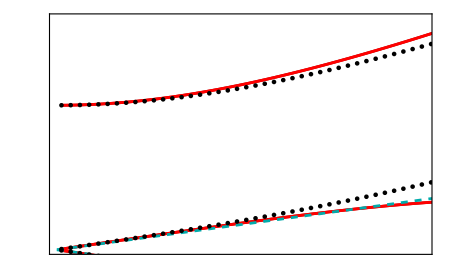

```mathematica
plot1 = Show[
  ListPlot[
   Table[Table[{2 π qlist[[n]], 
      2 π Re[gappedModesSelected[[n, m]]]}, {m, 1, 
      Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}], 
   PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, 
   PlotRange -> {{0, 4}, {0, 6}}, BaseStyle -> texStyle, 
   FrameLabel -> MaTeX[{"q/T", "\\Re\\omega/T"}, Magnification -> 1.4],
    FrameTicks -> {{yticks, None}, {xticks, None}}], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, 
      2 π Re[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Darker@Red, PlotRange -> All], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, -2 π Re[
        OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Red, PlotRange -> All], 
  Plot[{Re[
     2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]], 
    Re[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, 
   PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}], 
  ListPlot[
   Table[Transpose[{2 π qlist, 2 π Re[QNMs[[;; , n]]]}], {n, 
     1, 4}], PlotStyle -> Black]]
```

```mathematica
tickLabelsClean[{a_,b_,s_}]:=Table[{x,MaTeX[ToString@NumberForm[If[Abs[x]>=10^-15,x,0.0],{3,1}],Magnification->1.4]},{x,a,b,s}];

{xticks,yticks}=Switch[backgroundNumber,1,{tickLabels[{0,7,1}],tickLabels[{-12,0,2}]},2,{tickLabels[{0,4,1}],tickLabels[{-2.5,0,0.5}]},3,{tickLabels[{0,6,1}],tickLabels[{-3.0,0.5,0.5}]},4,{tickLabels[{0,10,2}],tickLabels[{-3.0,1.,1.}]},5,{tickLabels[{0,4,1}],tickLabelsClean[{-3.0,1.0,0.2}]},6,{tickLabels[{0,4,1}],tickLabels[{-0.8,0,0.2}]},7,{tickLabels[{0,10,2}],tickLabels[{-18,2,2}]}];

range=Switch[backgroundNumber,1,{{0,7},{-13,0}},2,{{0,4},{-2.5,0}},3,{{0,6},{-1.5,0.6}},4,{{0,10},{-3,1.7}},5,{{0,4},{-1,0.2}},6,{{0,4},{-0.8,0}},7,{{0,10},{-18,2}}];
```

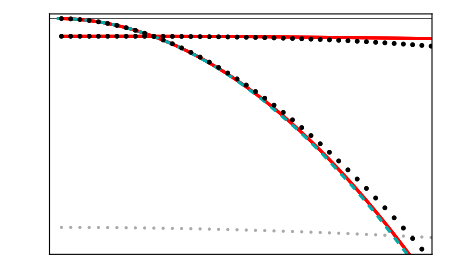

```mathematica
plot2 = Show[
  ListPlot[
   Table[Table[{2 π qlist[[n]], 
      2 π Im[gappedModesSelected[[n, m]]]}, {m, 1, 
      Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}], 
   PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, 
   PlotRange -> range, BaseStyle -> texStyle, 
   FrameLabel -> MaTeX[{"q/T", "\\Im\\omega/T"}, Magnification -> 1.4],
    GridLines -> {None, {0}}, GridLinesStyle -> Directive[Black], 
   FrameTicks -> {{yticks, None}, {xticks, None}}], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, 
      2 π Im[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Red, PlotRange -> All], 
  ListLinePlot[
   Table[Transpose[{2 π qlist, 
      2 π Im[OrderedModesL[[;; , n]]]}], {n, 1, 4}], 
   PlotStyle -> Red, PlotRange -> All], 
  Plot[{Im[
     2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]], 
    Im[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], 
       TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, 
   PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}], 
  ListPlot[
   Table[Transpose[{2 π qlist, 2 π Im[QNMs[[;; , n]]]}], {n, 
     1, 4}], PlotStyle -> Black]]
```

```mathematica
(*Export["/Users/mikel/Documents/figs-spinodal/QNM-vs-EFT/phiM=0.8/Re-" \
<> ToString[backgroundNumber] <> ".pdf", plot1, 
  ImageResolution -> 300];
Export["/Users/mikel/Documents/figs-spinodal/QNM-vs-EFT/phiM=0.8/Im-" \
<> ToString[backgroundNumber] <> ".pdf", plot2, 
  ImageResolution -> 300];*)
```

### Comparison between QNMs and EFT for the 6 backgrounds - figures for theory A

```mathematica
BackgroundIndeces = {49, 82, 92, 116, 160, 170};
ψHlist[[BackgroundIndeces[[1 ;; 6]]]]
```

{0.673755207946953999245044676811183839713814467855244852917724539604254209214946302863790765630167194,0.95216869870170930076208353255466574433958134990198024444365556280355110659690815129151587882648196,1.05004571213365576298520001319201034621524114498923776857116540868118167316978449590302653993016826,1.28883654767540232890802157318114655503709879643745432752579662454978067860909226652138855507501934,1.64754476088886068926395293864422074108483102603068141079042035657520018462811146770491037804844792,1.70010489071453947376803500633185022125812160493436815748034666407150643150376129008117700569524055}

General::munfl: 42.1039 1.6099210706904626578851737827365865980366947041079505667307286810234118920593307590862824868287×10^-361 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.24838 2.3182863417942662273546502471406847011728403739154488160922493006737131245654362930842467810334×10^-357 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 441.989 6.64041886146509776297134079732562503556874787711271258033538540995358998051831016588862521693811805×10^-358 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

background 1:  ψH = 0.6738,  n = 49

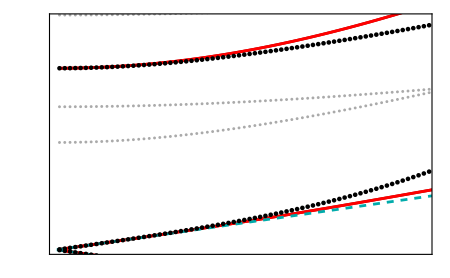
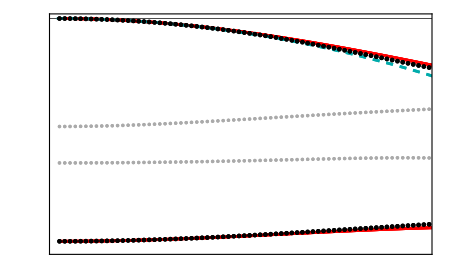

background 2:  ψH = 0.9522,  n = 82

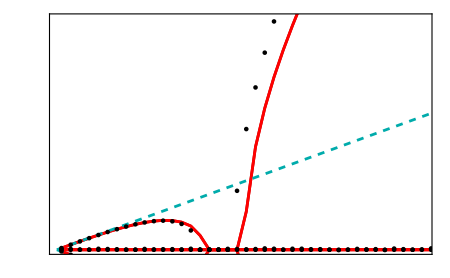
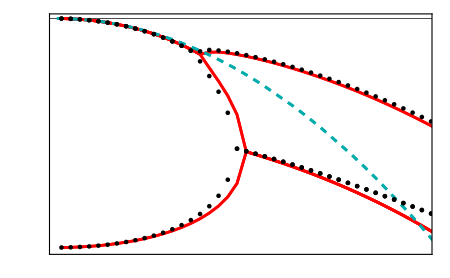

background 3:  ψH = 1.05,  n = 92

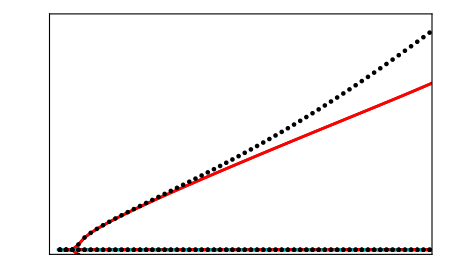
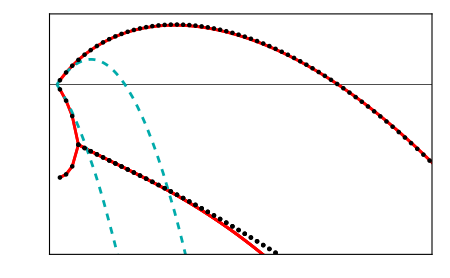

background 4:  ψH = 1.289,  n = 116

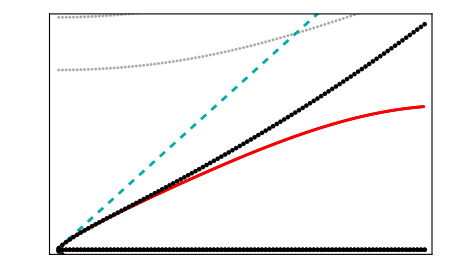
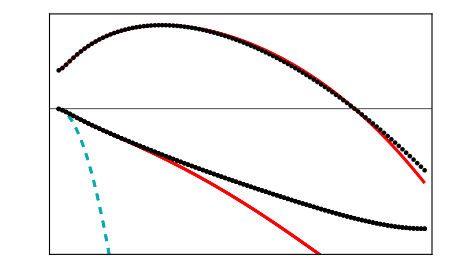

background 5:  ψH = 1.648,  n = 160

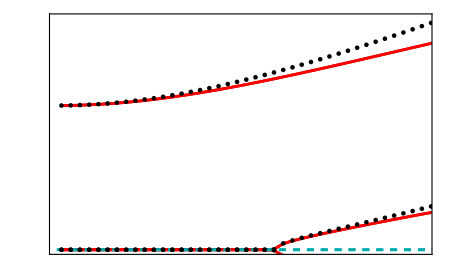
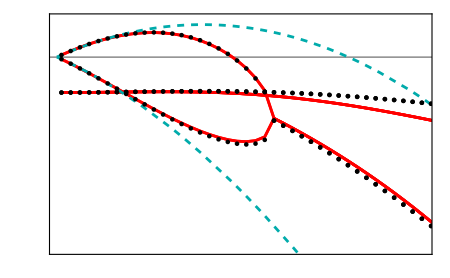

background 6:  ψH = 1.7,  n = 170

-Graphics--Graphics-

{./figs/QNM-vs-EFT/phiM=0.8/Im-1.pdf,./figs/QNM-vs-EFT/phiM=0.8/Im-2.pdf,./figs/QNM-vs-EFT/phiM=0.8/Im-3.pdf,./figs/QNM-vs-EFT/phiM=0.8/Im-4.pdf,./figs/QNM-vs-EFT/phiM=0.8/Im-5.pdf,./figs/QNM-vs-EFT/phiM=0.8/Im-6.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-1.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-2.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-3.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-4.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-5.pdf,./figs/QNM-vs-EFT/phiM=0.8/Re-6.pdf}

```mathematica
InterIndexList = {17, 17, 17, 17, 17, 17};
figDir = "./figs/QNM-vs-EFT/phiM=" <> ToString[N[ϕM /. constants]] <> "/";
Quiet[CreateDirectory[figDir, CreateIntermediateDirectories -> True]];
Quiet[CreateDirectory["./QNM vs EFT data/phiM=0.8", CreateIntermediateDirectories -> True]];
tickLabels[{a_, b_, s_}] := Table[{x, MaTeX[ToString@NumberForm[x, {3, 1}], Magnification -> 1.4]}, {x, a, b, s}];
tickLabelsClean[{a_, b_, s_}] := Table[{x, MaTeX[ToString@NumberForm[If[Abs[x] >= 10^-15, x, 0.0], {3, 1}], Magnification -> 1.4]}, {x, a, b, s}];

distinctNearest[list_, targets_] := Module[{avail = list, out = {}, id}, Do[id = First[Ordering[Abs[avail - t], 1]]; AppendTo[out, avail[[id]]]; avail = Delete[avail, id], {t, targets}]; out];
Do[
  (* background *)
  number = BackgroundIndeces[[backgroundNumber]];
  T = thermo[[number, 1]];
  e = thermo[[number, 5]];
  Λ = thermo[[number, 3]];
  {qmin, qmax} = {5/100, 10};
  Nq = 100;
  qlist = 1/(2 π) Range[qmin, qmax, (qmax - qmin)/(Nq - 1)];
  InterIndex = InterIndexList[[backgroundNumber]];

  (* EFT modes*)
  EFTModes = Table[𝓌 /. NSolve[dispEFT[[number]] /. 𝓆 -> qlist[[n]], 𝓌], {n, 1, Nq}];
  OrderedModesL = {};
  aux = EFTModes[[1]];
  Do[
    aux = distinctNearest[EFTModes[[n, ;;]], aux];
    AppendTo[OrderedModesL, aux];
    , {n, 1, Nq}];
  OrderedModesR = {};
  aux = EFTModes[[-1]];
  Do[
    aux = distinctNearest[EFTModes[[Nq - n, ;;]], aux];
    AppendTo[OrderedModesR, aux];
    , {n, 0, Nq - 1}];
  OrderedModesR = Reverse[OrderedModesR];
  OrderedModesInter = {};
  aux = EFTModes[[InterIndex]];
  Do[
    aux = distinctNearest[EFTModes[[n, ;;]], aux];
    AppendTo[OrderedModesInter, aux];
    , {n, InterIndex, 1, -1}];
  OrderedModesInter = Reverse[OrderedModesInter];
  aux = OrderedModesInter[[-1]];
  Do[
    aux = distinctNearest[EFTModes[[n, ;;]], aux];
    AppendTo[OrderedModesInter, aux];
    , {n, InterIndex + 1, Nq}];

  (* QNMs *)
  NQNMs = 0; eigenfunctions = False;
  gap = 10^-3;
  qcutoff = 1/(2 π) 1;
  QNMs = {};
  gappedModes = {};
  solnumber = 0;
  ImωgappedCutoff = 5;
  tol = 10^-1;
  Do[solnumber += 1;
    q = qlist[[n]];
    QNM1 = GetQNM[grid, fields[[number]], VV, q, T, prec, NQNMs, eigenfunctions];
    If[Abs[q] < qcutoff, modes = EFTModes[[n]];, modes = QNMs[[-1]];];
    aux = {}; avail = QNM1; 
    Do[
      id = First[Ordering[Abs[avail - modes[[i]]], 1]];
      AppendTo[aux, avail[[id]]];
      avail = Delete[avail, id];
      , {i, 1, Length[modes]}];
    AppendTo[QNMs, aux];
    AppendTo[gappedModes, Select[QNM1, Abs[Im[#]] <= ImωgappedCutoff && # != ∞ && # != 0 && Abs[Im[#]] >= tol &]];
    , {n, 1, Nq}];
  Clear[aux, id, q, QNM1];
  Export["./QNM vs EFT data/phiM=0.8/Modes-background-" <> ToString[backgroundNumber] <> ".m", {qlist, gappedModes, OrderedModesL, OrderedModesR, OrderedModesInter, QNMs}];

  (* Comparison between QNMs and EFT *)
  gappedModesSelected = Table[Select[gappedModes[[n]], Abs[Im[#]] <= 3 &], {n, 1, Nq}];
  {xticks, yticks} = Switch[backgroundNumber,
     1, {tickLabels[{0, 7, 1}], tickLabels[{0, 15, 5}]},
     2, {tickLabels[{0, 4, 1}], tickLabels[{0, 1, 0.2}]},
     3, {tickLabels[{0, 6, 1}], tickLabels[{0, 6, 1}]},
     4, {tickLabels[{0, 10, 2}], tickLabels[{0, 10, 2}]},
     5, {tickLabels[{0, 4, 1}], tickLabels[{0, 5, 1}]},
     6, {tickLabels[{0, 4, 1}], tickLabels[{0, 6, 1}]}];
  range = Switch[backgroundNumber, 1, {{0, 7}, {0, 16}}, 2, {{0, 4}, {0, 1}}, 3, {{0, 6}, {0, 6}}, 4, {{0, 10}, {0, 10.6}}, 5, {{0, 4}, {0, 5}}, 6, {{0, 4}, {0, 6}}];
  plot1 = Show[
    ListPlot[Table[Table[{2 π qlist[[n]], 2 π Re[gappedModesSelected[[n, m]]]}, {m, 1, Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}],
     PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, PlotRange -> range, BaseStyle -> texStyle,
     FrameLabel -> MaTeX[{"q/T", "\\Re\\omega/T"}, Magnification -> 1.4],
     FrameTicks -> {{yticks, None}, {xticks, None}}],
    ListLinePlot[Table[Transpose[{2 π qlist, 2 π Re[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Darker@Red, PlotRange -> All],
    ListLinePlot[Table[Transpose[{2 π qlist, -2 π Re[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Red, PlotRange -> All],
    Plot[{Re[2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], TΓThermo[[number]]]], Re[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}],
    ListPlot[Table[Transpose[{2 π qlist, 2 π Re[QNMs[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Black]];
  yticks = Switch[backgroundNumber,
     1, tickLabels[{-12, 0, 2}],
     2, tickLabels[{-2.5, 0, 0.5}],
     3, tickLabels[{-3.0, 0.5, 0.5}],
     4, tickLabels[{-2.0, 1., 1.}],
     5, tickLabelsClean[{-3.0, 1.0, 0.2}],
     6, tickLabels[{-0.8, 0, 0.2}]];
  range = Switch[backgroundNumber, 1, {{0, 7}, {-12.5, 0}}, 2, {{0, 4}, {-2.5, 0}}, 3, {{0, 6}, {-1.5, 0.6}}, 4, {{0, 10}, {-2.5, 1.6}}, 5, {{0, 4}, {-1, 0.2}}, 6, {{0, 4}, {-0.8, 0}}];
  plot2 = Show[
    ListPlot[Table[Table[{2 π qlist[[n]], 2 π Im[gappedModesSelected[[n, m]]]}, {m, 1, Length[gappedModesSelected[[n, ;;]]]}], {n, 1, Nq}],
     PlotStyle -> Lighter@Gray, Frame -> True, ImageSize -> 450, PlotRange -> range, BaseStyle -> texStyle,
     FrameLabel -> MaTeX[{"q/T", "\\Im\\omega/T"}, Magnification -> 1.4], GridLines -> {None, {0}}, GridLinesStyle -> Directive[Black],
     FrameTicks -> {{yticks, None}, {xticks, None}}],
    ListLinePlot[Table[Transpose[{2 π qlist, 2 π Im[OrderedModesInter[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Red, PlotRange -> All],
    ListLinePlot[Table[Transpose[{2 π qlist, 2 π Im[OrderedModesL[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Red, PlotRange -> All],
    Plot[{Im[2 π 𝓌Hydro[k/(2 π), cs2Thermo[[number]], TΓThermo[[number]]]], Im[2 π 𝓌Hydro[-k/(2 π), cs2Thermo[[number]], TΓThermo[[number]]]]}, {k, 0, 2 π qmax}, PlotStyle -> {{RGBColor[0, 0.67, 0.67], Dashed}}],
    ListPlot[Table[Transpose[{2 π qlist, 2 π Im[QNMs[[;; , n]]]}], {n, 1, 4}], PlotStyle -> Black]];

  Export[figDir <> "Re-" <> ToString[backgroundNumber] <> ".pdf", plot1, ImageResolution -> 300];
  Export[figDir <> "Im-" <> ToString[backgroundNumber] <> ".pdf", plot2, ImageResolution -> 300];
  Print[Row[{"background ", backgroundNumber, ":  ψH = ", N[ψHlist[[number]], 4], ",  n = ", number}]];
  Print[Row[{plot1, plot2}]];
  , {backgroundNumber, 1, 6}];
FileNames["*.pdf", figDir]
```